```mathematica
Names["mshtensorial`*"]
Remove["Global`*"]
"packagefile=msh_tensorial.wlファイルをおいているホルダーを表記\\msh_tensorial.wl" 
packagefile="C:\\Users\\shina\\Desktop\\math_tensor\\msh_tensorial.wl";

"パッケージmsh_tensorial.wlをダウンロードする。"
Needs["mshtensorial`",packagefile];
Names["Global`*"]
"パッケージ内いの関数と特殊文字を表記"
Names["mshtensorial`*"]
```

{}

Remove::rmnsm: "Global`*"に合致するシンボルはありません．

packagefile=msh_tensorial.wlファイルをおいているホルダーを表記\msh_tensorial.wl

パッケージmsh_tensorial.wlをダウンロードする。

{packagefile}

パッケージ内いの関数と特殊文字を表記

{AbsoluteDerivative,Christoffel1,Christoffel2,CovariantDerivative,DummyVariableSimplify,EinsteinTensor,EvaluateIndexDerivative,Expand2ndCODer,ExpandABSDer,ExpandChristoffel1,ExpandChristoffel2,ExpandCODer,ExpandDoubleIndex,ExpandIndex,ExpandMat,ExpandRCC,ExpandRiccFor,ExpandRicci,IndexDerivative,IndexDerivativeSimplify,IndexDerivativeUp,Kronecker,KroneckerSimplify,LeviCivitaRule,MatTen,MetricSimplify,NDim,OrderChristoffel,OrderIndexDeri,OrderTensor,RCC,RiccFormula,RieChrisCur,SetSystem,SetTensorRule,Tensor,TensorSimplify,ToContravariantIndex,ToCovariantIndex,Void,x,Γ,δ,ϵ,ξ,ρ,σ}

## 第７章 一般相対性理論

リーマン幾何学と言えば、最大の応用分野は一般相対性理論である。本章では、一般相対性理論に限って、リーマン幾何学について述べよう。

## 7.1 等価原理

### 一般相対性理論とは重力を扱う理論である。特殊相対性理論で、電磁気を中心とした力を扱っているのに、重力を扱わなかったのは、アインシュタインの心の中に、当初から重力は一般の力とは別であるという意識があったのだと思われる。その主たる原因は、重力質量mG と慣性質量mI の一致である。何故どんな質量の物体でも、同じ軌跡で落下するのであろうかという疑問に対し、アインシュタインは、空間の構造に起因するから、こうなると考えたのである。空間と言っても時間軸を含めた四次元空間である。本稿をお読みの方はどなたも重力がF = mg で与えられ、ニュートンの第二法則がF = maで与えられていることをご存知であろう。しかし、この二つのm が何故共通の値なのかを疑った人は意外に少いのではないだろうか。私も疑わなかった者の一人である。生活体験から、重いものや軽いものがあることは分っていたのでF = mg は簡単に理解できる。一方、私はガリレーの落下実験や惑星の運動などから、何故、これらは質量に依らず同じような軌跡を描くのだろうという疑問を感じたことはあった。そして、F = ma の式を見て、なるほど、だから物体は質量に依らない運動をするのだと納得してしまったのである。もちろん、その瞬間は何故同じm を使うのだろうという疑義は頭をよぎったのであるが、かなり早いうちにその疑問は維持されることなく消え去ったという気がする。ここにこだわり続けたアインシュタインは正に凄いとしか評価できない。

### より具体的には、重力のある空間で、自由落下しているエレベーターを考えると、その中では重力は感じられない。つまり、エレベータ内は慣性系（inertial system）になっている。このエレベーター内にいる人間は、自分が加速系にいて重力落下をしているか、慣性系にいるのかを区別する方法はない。また、エレベーター内で等速度運動をしているどんな質量の物体も、外から見ると、すべて同じ加速度で落下しているように見える。つまり、重力とはこれら二つの系の座標変換の結果、現われてくる量であると考えたのである。エレベータの思考実験の結果、エレベータ内では光も直線運動するはずである。ということは、重力のある系で観測すると、光も質量のある物質と同じように、放物線を描くことになる。光の落下が簡単には観測できないのは、光が余りにも高速すぎて、落下量よりも水平移動距離の方が著しく大きいからであろう。

### さて、質量があろうとなかろうと重力の影響を受けるとすると、これは球面幾何学のように空間が歪んでいると理解する方が自然である。つまり物体も光線もこの曲った空間の測地線に沿って移動しているだけではないだろうか。こうした大胆な仮説に基づいて、重力と空間歪の関係を求め、さらには重力の源泉である質量(特殊相対性理論の結論から、質量というよりはエネルギーと呼ぶ方がよい) と空間歪との関係を導出したものが、一般相対性理論である。このように、適切な座標系を選ぶことで、特殊相対性理論が働く慣性系（inertial system）が得られることを、等価原理（equivalence principle）と呼ぶ。

### 等価原理とは、重力場のなかで、すべての物体が、質量に依存せず、同じ重力加速度で運動することであるとも言える。そこで、等価原理の証明にはmG/mI が一定であることを実証すればよい。古くはガリレオのピサの斜塔での自由落下実験があるが、より正確には振子の錘の質量を変える、あるいは捻れの平衡などの方法がある。捻れの平衡について、若干説明しよう。地上の質点には重力以外に遠心力のような加速力が働く。前者はmI に、後者はmG に比例する。二つの異なる質点を用意し、この二つを棒で繋いで、適切な位置に支点をとり、下向きに働く重力に対して平衡をとる。これらの質点には地軸と垂直に加速力も働いているので、もし、重力質量と慣性質量に差があると、加速力の方では平衡がとれないことになり、この天秤は回転を初める。この回転のトルクを調べることにより、二つの質点のmG/mI に差があるかを調べることができる。この実験の結果、現在11 桁の確度で、質量比は一定と言える。つまり、等価原理は成立している可能性が高いのである。

## 7.2 測地線と重力場中の質点の運動

### 等価原理から考えると、重力場の影響下における物体の運動は、慣性系と異なる計量テンソルを持つ空間の測地線で表されそうでる。測地線の式(5.17) を再掲しておこう。ただし、物体の運動の軌道に沿っては、ds2 < 0 となるため、s の代わりに、c^2dτ^2 = −ds^2 の関係にある cτ を使うことにする。そこで (ẋ)_(" ")^m==∂_τ dx_(" ")^m となるが、式 (5.17) の両辺を −1 で除すと同じ形になる。

```mathematica
Remove["Global`*"]
ClearAttributes[Times,Orderless]
ClearAttributes[Plus,Orderless]
Tensor[ẋ,{Void},{m}]==IndexDerivative[Tensor[dx,{Void},{m}],τ]

s1=Tensor[ẍ,{Void},{k}]+Christoffel2[g,x][{m,n},{k}]Tensor[ẋ,{Void},{m}]Tensor[ẋ,{Void},{n}]==0
"(7.1)"
Tensor[ẍ,{Void},{1}]+HoldForm[Christoffel2[g,x][{0,0},{1}]]c^2==0
-IndexDerivative[ϕ,x[1]]+HoldForm[Christoffel2[g,x][{0,0},{1}]]c^2==0
HoldForm[Christoffel2[g,x][{0,0},{1}]]==IndexDerivative[ϕ,x[1]]/c^2
```

(ẋ)_^m==∂_τ dx_^m

(ẍ)_^k+Γ_mn^k (ẋ)_^m (ẋ)_^n==0

(7.1)

(ẍ)_^1+Γ_00^1 (c)^2==0

-∂_(x_^1) ϕ+Γ_00^1 (c)^2==0

Γ_00^1==(∂_(x_^1) ϕ)/(c)^2

### ただし、 Γ_mn^(" "k)もdcτ^2 から誘導したもの(実はds2 から誘導したものと同じ) になる。以後、物体の運動を議論する場合には、ds^2 ではなくdcτ2 を計量とすることとする。測地線の方程式も、重力下におけるニュートンの方程式と同じく二階の微分方程式であり、同じ数の自由度を持っている。問題を簡単にするために、光速に比べ十分低速の粒子を対象にしよう。この仮定により dτ ≑dt とできる。また、ẋ= dx/dτ などは cṫ= dct/dτ ≑c に比べ、圧倒的に小さいと言える。すると、上式(7.1) のΓ_mn^(" "k) の効果はΓ_00^(" "k) のみしか効いてこないことがわかる。

```mathematica
Remove["Global`*"]
Christoffel2[g,x][{m,n},{k}]
Tensor[ẍ,{Void},{k}]+Christoffel2[g,x][{0,0},{k}]Tensor[ẋ,{Void},{0}]Tensor[ẋ,{Void},{0}]==0
Tensor[ẍ,{Void},{k}]+Christoffel2[g,x][{0,0},{k}](c ṫ)^2==0
```

Γ_mn^k

(ẍ)_^k+Γ_00^k ((ẋ)_^0)^2==0

(ẍ)_^k+Γ_00^k (c)^2 (ṫ)^2==0

### さて、重力が x_(" ")^1方向にしかかからないとして、この式がニュートンの式と近似的に一致するにはどうしたらよいだろうか。ニュートンの式は、重力ポテンシャルをϕ(x_(" ")^1) とするとき、d^2x_(" ")^1/dt^2 = −∂1ϕである。幸いにして、低速におけるc ṫはほぼc であるのでΓ_00^(" "k) の項はk = 1 に対してだけ存在すればよい。さらに、 (ẍ)_(" ")^1≑d^2x_(" ")^1/dt^2 = −∂1ϕで、これと Γ_00^(" "1)c^2の和が0 であることより、Γ_00^(" "1)= (1/c2) ∂1ϕが得られる。この他の空間座標方向には加速はないため、k = 2, 3 に対して Γ_mn^(" "k)= 0 となる。

```mathematica
Tensor[ẍ,{Void},{1}]+HoldForm[Christoffel2[g,x][{0,0},{1}]]c^2==0
-IndexDerivative[ϕ,x[1]]+HoldForm[Christoffel2[g,x][{0,0},{1}]]c^2==0
HoldForm[Christoffel2[g,x][{0,0},{1}]]==IndexDerivative[ϕ,x[1]]/c^2
```

(c)^2 Γ_00^1+(ẍ)_^1==0

(c)^2 Γ_00^1-∂_(x_^1) ϕ==0

Γ_00^1==(∂_(x_^1) ϕ)/(c)^2

### 次にdcτ2 の計量テンソルg_mn^(" "" ")を推定してみよう。g_mn^(" "" ") は慣性系の値diag[1,−1,−1,−1]とほとんど等しく、僅かなずれしかないものとしよう。すると、計量テンソルから接続係数を求める式(5.10) より、∂_(x_(" ")^0) g_01^(" "" ")、∂0g10,∂_(x_(" ")^1) g_00^(" "" ") の三項しか値を持ちえない。g_mn^(" "" ") はx 軸方向にしか変動していないだろうから、g_00^(" "" ") だけが存在することになる。つまり、次式が得られる。

```mathematica
Remove["Global`*"]
SetAttributes[Times,Orderless]
SetAttributes[Plus,Orderless]
x[1]
Tensor[ẍ,{Void},{1}]
Tensor[g,{m,n},{Void,Void}]
Christoffel2[g,x][{m,n},{k}]
HoldForm[Christoffel2[g,x][{0,0},{1}]]==-1/2 Tensor[g,{Void,Void},{1,1}]IndexDerivative[Tensor[g,{Void,Void},{0,0}],x[1]]==1/c^2IndexDerivative[ϕ,x[1]]
```

x_^1

(ẍ)_^1

g_mn^

Γ_mn^k

Γ_00^1==-1/2 ∂_(x_^1) g_^00 g_^11==(∂_(x_^1) ϕ)/(c)^2

```mathematica
Christoffel2[g,x][{0,0},{1}]
%/.Tensor[g,{0,1},{Void,Void}]->0/.Tensor[g,{0,2},{Void,Void}]->0/.Tensor[g,{0,3},{Void,Void}]->0
s8=HoldForm[Christoffel2[g,x][{0,0},{1}]]==(%/.Tensor[g,{Void,Void},{1,2}]->0/.Tensor[g,{Void,Void},{1,3}]->0)==1/c^2IndexDerivative[ϕ,x[1]]
```

1/2 (-∂_(x_^1) g_00^+2 ∂_(x_^0) g_01^) g_^11+1/2 (-∂_(x_^2) g_00^+2 ∂_(x_^0) g_02^) g_^12+1/2 (-∂_(x_^3) g_00^+2 ∂_(x_^0) g_03^) g_^13

-1/2 ∂_(x_^1) g_00^ g_^11-1/2 ∂_(x_^2) g_00^ g_^12-1/2 ∂_(x_^3) g_00^ g_^13

Γ_00^1==-1/2 ∂_(x_^1) g_00^ g_^11==(∂_(x_^1) ϕ)/(c)^2

### g_(" "" ")^11 がほぼ−1 であるので、 g_(" "" ")^00= (2/c^2) ϕ(x) + const が得られる。重力中心より十分遠方では、重力のないときのg_00^(" "" ")= 1 に漸近しなければないので、次の結果が得られる。

```mathematica
s8[[2;;3]]/.Tensor[g,{Void,Void},{1,1}]->-1
Tensor[g,{Void,Void},{0,0}]==1+2 ϕ/c^2
```

1/2 ∂_(x_^1) g_00^==(∂_(x_^1) ϕ)/(c)^2

g_^00==1+(2 ϕ)/(c)^2

### これ以外のgmn はδmn に等しいので、線素は次式のようになる。

```mathematica
dcτ^2==(1+2 ϕ/c^2)(dct)^2-(dx^2+dy^2+dz^2)
%[[1]]/dτ^2==(%[[2]]/dτ^2//Expand)
c^2==%[[2]] /.(dx/dτ)^2->Tensor[v,{Void},{1}]^2/.(dy/dτ)^2->Tensor[v,{Void},{2}]^2/.(dz/dτ)^2->Tensor[v,{Void},{3}]^2/.(dct /dτ)^2->Tensor[v,{Void},{0}]^2/.ϕ->-g  x[1]
s3=c^2==Factor[%[[2,{1,5}]]]+%[[2,2;;4]]
```

(dcτ)^2==-(dx)^2-(dy)^2-(dz)^2+(dct)^2 (1+(2 ϕ)/(c)^2)

(dcτ)^2/(dτ)^2==(dct)^2/(dτ)^2-(dx)^2/(dτ)^2-(dy)^2/(dτ)^2-(dz)^2/(dτ)^2+(2 (dct)^2 ϕ)/((c)^2 (dτ)^2)

(c)^2==(v_^0)^2-(v_^1)^2-(v_^2)^2-(v_^3)^2-(2 g (v_^0)^2 x_^1)/(c)^2

(c)^2==-(v_^1)^2-(v_^2)^2-(v_^3)^2+((v_^0)^2 ((c)^2-2 g x_^1))/(c)^2

### 改めて、これらのgmn からスタートして測地線の方程式を解いておく価値があろう。特にϕ= −gx1（x1 の原点は、観測している付近とする）の場合を扱ってみよう。Γkmn はΓ100 = −g/c2、Γ001 = Γ010 = −g/[c2(1−2gx1/c2)] を除いてすべて0 となる。そこで、k = 0, 1に対する測地線方程式は、vk = x˙k として、次式のようになる。

```mathematica
Tensor[dv,{Void},{0}]/dτ-2 g/c^2/(1-2 g x[1]/c^2)Tensor[v,{Void},{0}]Tensor[v,{Void},{1}]==0
"(7.3)"
Tensor[dv,{Void},{2}]/dτ-g/c^2Tensor[v,{Void},{0}]^3==0
"(7.4)"
```

dv_^0/dτ-(2 g v_^0 v_^1)/((c)^2 (1-(2 g x_^1)/(c)^2))==0

(7.3)

dv_^2/dτ-(g (v_^0)^3)/(c)^2==0

(7.4)

### 式(7.3) の両辺をv0 で割って、τ で積分すると、

```mathematica
d(Log[Tensor[v,{Void},{0}]])/dτ+d Log[1-2 g x[1]/c^2]/dτ==0
Tensor[v,{Void},{0}](1-2 g x[1]/c^2)==Tensor[v,{Void},{0}][0]
s4=Solve[%,Tensor[v,{Void},{0}]]
```

(d Log[v_^0])/dτ+(d Log[1-(2 g x_^1)/(c)^2])/dτ==0

v_^0 (1-(2 g x_^1)/(c)^2)==v_^0[0]

{{v_^0→((c)^2 v_^0[0])/((c)^2-2 g x_^1)}}

### 積分定数v_(" ")^0[0] はx_(" ")^1 = 0 におけるv0 である。これから得られた v_(" ")^0を式(7.4) へ代入すると、x_(" ")^1 だけの微分方程式が得られるが、容易には解けない。そこで、今迄の例で度々行ったように、線素の式を利用しよう。dcτ2 の定義式の両辺をdτ2 で除すと、

```mathematica
c^2==(1-2 g x[1]/c^2)Tensor[v,{Void},{0}]^2-(Tensor[v,{Void},{1}]^2+Tensor[v,{Void},{2}]^2+Tensor[v,{Void},{3}]^2)
%/.Tensor[v,{Void},{2}]->Tensor[v,{Void},{2}][0]/.Tensor[v,{Void},{3}]->Tensor[v,{Void},{3}][0]/.s4
s2=Simplify[%]
```

(c)^2==-(v_^1)^2-(v_^2)^2-(v_^3)^2+(v_^0)^2 (1-(2 g x_^1)/(c)^2)

{(c)^2==-(v_^1)^2+((c)^4 (1-(2 g x_^1)/(c)^2) (v_^0[0])^2)/(((c)^2-2 g x_^1)^2)-(v_^2[0])^2-(v_^3[0])^2}

{(c)^2+(v_^1)^2+(v_^2[0])^2+(v_^3[0])^2==((c)^2 (v_^0[0])^2)/((c)^2-2 g x_^1)}

### v2 = v2(0)、v3 = v3(0) なので、

```mathematica
s3=Solve[s2,Tensor[v,{Void},{1}]]//Simplify
```

{{v_^1→-((2 g x_^1 ((c)^2+(v_^2[0])^2+(v_^3[0])^2)-(c)^2 ((c)^2-(v_^0[0])^2+(v_^2[0])^2+(v_^3[0])^2))^(1/2))/(((c)^2-2 g x_^1)^(1/2))},{v_^1→((2 g x_^1 ((c)^2+(v_^2[0])^2+(v_^3[0])^2)-(c)^2 ((c)^2-(v_^0[0])^2+(v_^2[0])^2+(v_^3[0])^2))^(1/2))/(((c)^2-2 g x_^1)^(1/2))}}

### 残念ながら、この微分方程式は解けない。2gx1/c2 が1 に比べ十分小さい場合には1/(1 −2gx1/c2) ≑1 + 2gx1/c2 とすることで、解くことが可能である。

```mathematica
Tensor[v,{Void},{1}]/.s3[[2]]//Simplify
Expand[%^2]
Factor[%[[{1,2,4,5,6,7}]]]+%[[3]]
%/.%[[2,2]]->(2 g x[1]+c^2)/c^4
s6=Integrate[1/Sqrt[%],x[1]]==τ-τ0
```

((2 g x_^1 ((c)^2+(v_^2[0])^2+(v_^3[0])^2)-(c)^2 ((c)^2-(v_^0[0])^2+(v_^2[0])^2+(v_^3[0])^2))^(1/2))/(((c)^2-2 g x_^1)^(1/2))

-(c)^4/((c)^2-2 g x_^1)+(2 (c)^2 g x_^1)/((c)^2-2 g x_^1)+((c)^2 (v_^0[0])^2)/((c)^2-2 g x_^1)-((c)^2 (v_^2[0])^2)/((c)^2-2 g x_^1)+(2 g x_^1 (v_^2[0])^2)/((c)^2-2 g x_^1)-((c)^2 (v_^3[0])^2)/((c)^2-2 g x_^1)+(2 g x_^1 (v_^3[0])^2)/((c)^2-2 g x_^1)

-(c)^2+((c)^2 (v_^0[0])^2)/((c)^2-2 g x_^1)-(v_^2[0])^2-(v_^3[0])^2

-(c)^2+(((c)^2+2 g x_^1) (v_^0[0])^2)/(c)^2-(v_^2[0])^2-(v_^3[0])^2

((c)^2 (-(c)^2+(((c)^2+2 g x_^1) (v_^0[0])^2)/(c)^2-(v_^2[0])^2-(v_^3[0])^2)^(1/2))/(g (v_^0[0])^2)==τ-τ0

### これをx1 について解くと、

```mathematica
Solve[s6[[1]]^2==s6[[2]]^2,x[1]]
x[1]/.%[[1]]//Expand
s7=Factor[%[[3;;5]]]+Factor[%[[{1,2,6,7}]]]
```

{{x_^1→((c)^6-(c)^4 (v_^0[0])^2+(g)^2 (τ)^2 (v_^0[0])^4-2 (g)^2 τ τ0 (v_^0[0])^4+(g)^2 (τ0)^2 (v_^0[0])^4+(c)^4 (v_^2[0])^2+(c)^4 (v_^3[0])^2)/(2 (c)^2 g (v_^0[0])^2)}}

-(c)^2/(2 g)+(c)^4/(2 g (v_^0[0])^2)+(g (τ)^2 (v_^0[0])^2)/(2 (c)^2)-(g τ τ0 (v_^0[0])^2)/(c)^2+(g (τ0)^2 (v_^0[0])^2)/(2 (c)^2)+((c)^2 (v_^2[0])^2)/(2 g (v_^0[0])^2)+((c)^2 (v_^3[0])^2)/(2 g (v_^0[0])^2)

(g (τ-τ0)^2 (v_^0[0])^2)/(2 (c)^2)+((c)^2 ((c)^2-(v_^0[0])^2+(v_^2[0])^2+(v_^3[0])^2))/(2 g (v_^0[0])^2)

### これより、質点の運動方程式が得られる。

```mathematica
s7/.%[[2]]->x[1][0]
```

(g (τ-τ0)^2 (v_^0[0])^2)/(2 (c)^2)+x_^1[0]

### v0(0) ≑ c であるので、ほぼ、一定重力場の落下の式と一致する。

### 以上の議論から、質点の運動は重力場の影響を計量テンソルに反映させた歪んだ空間の測地線で表されることがわかった。また、g_mn^(" "" ") がほぼ慣性系における計量に等しい場合には、g_00^(" "" ")の位置依存性だけが重要であり、他の計量の位置依存性にはあまり関係せず、同じ結論が得られる。実際、後述のシュバルツシルト計量を見ると、g_11^(" "" ")は次のようであることが誘導される。

```mathematica
Tensor[g,{m,n},{Void,Void}]
Tensor[g,{0,0},{Void,Void}]
Tensor[g,{1,1},{Void,Void}]==(1+2 ϕ/c^2)^-1
```

g_mn^

g_00^

g_11^==(1+(2 ϕ)/(c)^2)^-1

## 7.3 アインシュタイン方程式

### 前節に述べた議論を一般化することで、一般相対性理論（general theory of relativity）を導出することができる。ニュートンの重力方程式をポアソン方程式で表すと、次式のようになる。

```mathematica
Tensor["∇",{},{2}]ϕ[x]==2 Pi G ρ[x]
"(7.5)"
```

∇_^2 ϕ[x]==2 G π ρ[x]

(7.5)

```mathematica
("∇")_^2 ϕ[x]==4 G π ρ[x]
```

∇_^2 ϕ[x]==4 G π ρ[x]

### ところで、ϕ(x) は式(7.2) より、計量テンソルに対応することから、この式の左辺は恐らく計量テンソルの二次微分になるであろう。また、右辺は質量密度、つまり特殊相対性理論の式(4.14) に示したエネルギー運動量テンソルT_(" "" ")^mn になることが予想できる。ただし、式(4.13)に示したエネルギー運動量の保存則は、空間微分が共変微分に変って、次のようになる。

```mathematica
CovariantDerivative[Tensor[T,{Void,Void},{m,n}],x,n,g]==0
CovariantDerivative[Tensor[T,{Void,Void},{m,n}],x,m,g]==0
```

∇_n^ T_^mn==0

∇_m^ T_^mn==0

```mathematica
RieChrisCur[{Void},{Void},{i,j},g,x]
ExpandRicci[%]/.ξ->k/.ρ->m/.σ->l
RieChrisCur[{Void},{Void},{Void},g,x]
ExpandRicci[%]/.ξ->k/.ρ->m/.σ->l
RieChrisCur[{i},{j},{Void},g,x]
ExpandRicci[%]/.ξ->k/.ρ->m/.σ->l
```

RCC_,^ij

RCC_(m,kl)^k g_^im g_^jl

RCC_,^

RCC_(m,kl)^k g_^ml

RCC_(i,j)^

RCC_(i,lj)^l

### 以下の式変形に都合のよいように、T_(" "" ")^mn の対称性より("∇")_m^(" ")の替りに("∇")_n^(" ") としている。右辺は全エネルギー運動量応力テンソル（total energy-momentum-stress tensor）そのものでよいが、左辺の候補としては、今迄議論した各章から計量テンソルの二次微分までを含むテンソルということになる。第5 章の共変微分で現われた接続係数はテンソルではない。第6章の曲率に示したいくつかの量には、計量テンソルの二次微分が含まれている。曲率テンソルおよびそれを縮約したリッチテンソルやスカラー曲率である。さらに、計量テンソル自身も0次微分のテンソルである。右辺が2 階のテンソルであるので、4 階の曲率テンソルは候補とならない。リッチテンソルRCC_(" "","" ")^(" "mn)は有力な候補である。またスカラー曲率に計量テンソルを掛けたRCC_(" "","" ")^(" "" ") g_(" "" ")^mn も候補となる。さらに計量テンソルg_(" "" ")^mn そのものも候補である。 このため、左辺をこれらの線形結合としてみよう。

```mathematica
s1=c1 RieChrisCur[{Void},{Void},{m,n},g,x]+c2 Tensor[g,{Void,Void},{m,n}] RieChrisCur[{Void},{Void},{Void},g,x]+c3 Tensor[g,{Void,Void},{m,n}]==c4 Tensor[T,{Void,Void},{m,n}]
```

c1 RCC_,^mn+c3 g_^mn+c2 RCC_,^ g_^mn==c4 T_^mn

### 右辺の共変微分が0 であることから左辺の共変微分も0 のはずである。

```mathematica
HoldForm[c1 CovariantDerivative[RieChrisCur[{Void},{Void},{m,n},g,x],x,m,g]+c2 CovariantDerivative[Tensor[g,{Void,Void},{m,n}] RieChrisCur[{Void},{Void},{Void},g,x],x,m,g]+c3 CovariantDerivative[Tensor[g,{Void,Void},{m,n}],x,m,g]]==CovariantDerivative[Tensor[T,{Void,Void},{m,n}],x,m,g]
s2=ReleaseHold[%]/.CovariantDerivative[Tensor[T,{Void,Void},{m,n}],x,m,g]->0
```

c1 (∇_m^ RCC_,^mn)+c2 (∇_m^ RCC_,^ g_^mn)+c3 (∇_m^ g_^mn)==∇_m^ T_^mn

c1 (∇_m^ RCC_,^mn)+c2 (∇_m^ RCC_,^) g_^mn==0

### まず、式(5.16) を縮約して("∇")_m^(" ")g_(" "" ")^mn = 0 である。また、式(6.9) および式(6.10) より、 ("∇")_m^(" ")RCC_(" "","" ")^(" "" ")g_(" "" ")^mn= 2 ("∇")_m^(" ")RCC_(" "","" ")^(" "mn)が成立するので、これらを上式に代入すると、

```mathematica
s2[[1]]/.s2[[1,2]]->2 c2 CovariantDerivative[RieChrisCur[{Void},{Void},{m,n},g,x],x,m,g]
Factor[%]
```

c1 (∇_m^ RCC_,^mn)+2 c2 (∇_m^ RCC_,^mn)

(c1+2 c2) (∇_m^ RCC_,^mn)

```mathematica
Remove["Global`*"]
"(6.9)"
Tensor[G,{Void,Void},{i,j}]==RieChrisCur[{Void},{Void},{i,j},g,x]-1/2 Tensor[g,{Void,Void},{i,j}]RieChrisCur[{Void},{Void},{Void},g,x]
"(6.10) アインシュタインテンソルの発散が０より p84 "
CovariantDerivative[Tensor[G,{Void,Void},{i,j}],x,i,g]==CovariantDerivative[RieChrisCur[{Void},{Void},{i,j},g,x],x,i,g]-1/2HoldForm[ CovariantDerivative[Tensor[g,{Void,Void},{i,j}]RieChrisCur[{Void},{Void},{Void},g,x],x,i,g]]==0
%[[2]]/.i->m/.j->n
Expand[2 %]
-%[[2]]==%[[1]]
```

(6.9)

G_^ij==RCC_,^ij-1/2 RCC_,^ g_^ij

(6.10) アインシュタインテンソルの発散が０より p84

∇_i^ G_^ij==∇_i^ RCC_,^ij-1/2 (∇_i^ RCC_,^ g_^ij)==0

∇_m^ RCC_,^mn-1/2 (∇_m^ RCC_,^ g_^mn)

2 (∇_m^ RCC_,^mn)-∇_m^ RCC_,^ g_^mn

∇_m^ RCC_,^ g_^mn==2 (∇_m^ RCC_,^mn)

### つまり、c2 = −c1/2 が得られる。したがって、

```mathematica
c1 RieChrisCur[{Void},{Void},{m,n},g,x]+c2 Tensor[g,{Void,Void},{m,n}] RieChrisCur[{Void},{Void},{Void},g,x]+c3 Tensor[g,{Void,Void},{m,n}]==c4 Tensor[T,{Void,Void},{m,n}]
%/.c2->-1/2 c1/.c4->K c1/.c3->-Λ c1
s4=Expand[%[[1]]/c1]==Expand[%[[2]]/c1]
```

c1 RCC_,^mn+c3 g_^mn+c2 RCC_,^ g_^mn==c4 T_^mn

c1 RCC_,^mn-c1 Λ g_^mn-1/2 c1 RCC_,^ g_^mn==c1 K T_^mn

RCC_,^mn-Λ g_^mn-1/2 RCC_,^ g_^mn==K T_^mn

### が得られる。Λ = −c3/c1,K = c4/c1 と置き換えている。 Λ g_(" "" ")^mnは宇宙項（cosmological term）と呼ばれ、宇宙のサイズになると影響が現われてくるが、アインシュタインも最後まで導入すべきかを迷った項である。またその係数Λ は、宇宙定数（cosmological constant）と呼ばれるが、いまだに値が定まっていない定数である(もしかすると0 かも知れない)。なお、式(4.16) に示した完全流体の応力テンソルを求めた際に、T_(" "" ")^mn にg_(" "" ")^mn を組み込んだように、宇宙項をT_(" "" ")^mn に組み込むことも可能である。本書ではその立場をとることとし、宇宙項は外した。(7.6)

```mathematica
"(7.6)"
s5=Tensor[G,{Void,Void},{m,n}]==(s4[[1]] /. Λ -> 0)==s4[[2]]
```

(7.6)

G_^mn==RCC_,^mn-1/2 RCC_,^ g_^mn==K T_^mn

### 最後のK はニュートンの重力場の方程式との対応から値を決めることができる。式(6.9)に示したアインシュタインテンソルG_(" "" ")^mn==RCC_(" "","" ")^(" "mn)-1/2 RCC_(" "","" ")^(" "" ") g_(" "" ")^mn を使うと、もう少し式を簡単に表すことが可能であるが、だからといって計算が簡単になるわけではないので、以後はこの形の式を利用する。 式(7.6) の両辺にg_mn^(" "" ") を掛けて縮約を行う。

```mathematica
Tensor[g,{m,n},{Void,Void}]s5[[2]]==Tensor[g,{m,n},{Void,Void}]s5[[3]]
RieChrisCur[{Void},{Void},{Void},g,x]-2 RieChrisCur[{Void},{Void},{Void},g,x]==%[[2]]
s6=%/.m->k/.n->l
```

(RCC_,^mn-1/2 RCC_,^ g_^mn) g_mn^==K g_mn^ T_^mn

-RCC_,^==K g_mn^ T_^mn

-RCC_,^==K g_kl^ T_^kl

### これから得られたR を式(7.6) へ代入すると、 (7.7)

```mathematica
"(7.7)"
s5[[{2,3}]]/.-s6[[1]]->-s6[[2]]
%[[1,1]]==Factor[-%[[1,2]]+%[[2]]]
```

(7.7)

RCC_,^mn+1/2 K g_^mn g_kl^ T_^kl==K T_^mn

RCC_,^mn==-1/2 K (g_^mn g_kl^ T_^kl-2 T_^mn)

### この式は式(7.6) と等価であるため、この式を使ってK を求めよう。 まず、重力場は十分小さいとすると、その計量テンソルへの影響も小さいだろうから、g_(" "" ")^mnのη_(" "" ")^mn (= diag(−1, 1, 1, 1)) からのずれは微小量である。接続係数も次のように近似できるだろう。

```mathematica
Remove["Global`*"]
GM=DiagonalMatrix[{-1,1,1,1}];
SetSystem[x,g,GM]
Tensor[g,{m,n},{Void,Void}]Tensor[g,{Void,Void},{n,m}]
ExpandDoubleIndex[%,{m,n}]
```

g_^nm g_mn^

4

```mathematica
Remove["Global`*"]
⟨Tensor[η,{Void,Void},{m,n}]⟩==DiagonalMatrix[{-1,1,1,1}]
Christoffel2[g ,x][{l,m},{k}]==ExpandChristoffel1[ExpandChristoffel2[Christoffel2[g ,x][{l,m},{k}]]]/.σ->n

Christoffel2[g ,x][{l,m},{k}]≃%[[2]]/.Tensor[g,{Void,Void},{k,n}]->Tensor[η,{Void,Void},{k,n}]
```

⟨η_^mn⟩=={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

Γ_lm^k==1/2 (-∂_(x_^n) g_lm^+∂_(x_^m) g_ln^+∂_(x_^l) g_mn^) g_^kn

Γ_lm^k≃1/2 (-∂_(x_^n) g_lm^+∂_(x_^m) g_ln^+∂_(x_^l) g_mn^) η_^kn

### さらに、リッチテンソルも次のように近似できる。

```mathematica
RieChrisCur[{m},{l},{Void},g,x]
ExpandRicci[%]/.σ->k
ExpandRCC[%]/.ρ->i
%/.%[[{3,4}]]->0
ExpandChristoffel2[%];
ExpandChristoffel1[%]/.σ->n//Expand;
%/.IndexDerivative[Tensor[g,{Void,Void},{i_,j_}],x[k_]]->0
OrderIndexDeri[%,x]/.Tensor[g,{Void,Void},{k,n}]->Tensor[η,{Void,Void},{k,n}]//Factor
```

RCC_(m,l)^

RCC_(m,kl)^k

-∂_(x_^l) Γ_km^k+∂_(x_^k) Γ_lm^k-Γ_km^i Γ_li^k+Γ_ki^k Γ_lm^i

-∂_(x_^l) Γ_km^k+∂_(x_^k) Γ_lm^k

1/2 ∂_(x_^n,x_^l) g_km^ g_^kn-1/2 ∂_(x_^m,x_^l) g_kn^ g_^kn-1/2 ∂_(x_^n,x_^k) g_lm^ g_^kn+1/2 ∂_(x_^m,x_^k) g_ln^ g_^kn-1/2 ∂_(x_^k,x_^l) g_mn^ g_^kn+1/2 ∂_(x_^l,x_^k) g_mn^ g_^kn

1/2 (∂_(x_^l,x_^n) g_km^-∂_(x_^l,x_^m) g_kn^-∂_(x_^k,x_^n) g_lm^+∂_(x_^k,x_^m) g_ln^) η_^kn

### ここで、接続係数の微分は十分小さいということで、その二乗の項は削除した。後述との関係からR00 だけを計算しよう。また、定常状態を考え∂0 = 0 としよう。

```mathematica
RieChrisCur[{0},{0},{Void},g,x]
ExpandRicci[%]/.σ->k
ExpandRCC[%]/.ρ->i
%/.%[[{3,4}]]->0
ExpandChristoffel2[%];
ExpandChristoffel1[%]/.σ->n//Expand
OrderIndexDeri[%,x]/.Tensor[g,{Void,Void},{k,n}]->Tensor[η,{Void,Void},{k,n}]//Factor
%/.IndexDerivative[w_,x[0]]->0/.IndexDerivative[w_,x[0],x[i_]]->0
%/.IndexDerivative[Tensor[η,{Void,Void},{k,n}],x[i_]]->0
1/2  Tensor["∇",{},{}]^2 Tensor[g,{0,0},{Void,Void}]
HoldForm[1/2Tensor["∇",{},{}]^2 (1+2 ϕ/c^2)]
HoldForm[1/c^2Tensor["∇",{},{}]^2  ϕ]
```

RCC_(0,0)^

RCC_(0,k0)^k

∂_(x_^k) Γ_00^k-∂_(x_^0) Γ_k0^k-Γ_(0i)^k Γ_k0^i+Γ_00^i Γ_ki^k

∂_(x_^k) Γ_00^k-∂_(x_^0) Γ_k0^k

-1/2 ∂_(x_^k) g_(0n)^ ∂_(x_^0) g_^kn-1/2 ∂_(x_^n) g_00^ ∂_(x_^k) g_^kn+∂_(x_^0) g_(0n)^ ∂_(x_^k) g_^kn+1/2 ∂_(x_^0) g_^kn ∂_(x_^n) g_k0^-1/2 ∂_(x_^0) g_^kn ∂_(x_^0) g_kn^-1/2 ∂_(x_^n,x_^k) g_00^ g_^kn+∂_(x_^0,x_^k) g_(0n)^ g_^kn-1/2 ∂_(x_^k,x_^0) g_(0n)^ g_^kn+1/2 ∂_(x_^n,x_^0) g_k0^ g_^kn-1/2 ∂_(x_^0,x_^0) g_kn^ g_^kn

1/2 (-∂_(x_^k) g_(0n)^ ∂_(x_^0) η_^kn+∂_(x_^n) g_k0^ ∂_(x_^0) η_^kn-∂_(x_^0) g_kn^ ∂_(x_^0) η_^kn-∂_(x_^n) g_00^ ∂_(x_^k) η_^kn+2 ∂_(x_^0) g_(0n)^ ∂_(x_^k) η_^kn-∂_(x_^k,x_^n) g_00^ η_^kn+∂_(x_^0,x_^k) g_(0n)^ η_^kn+∂_(x_^0,x_^n) g_k0^ η_^kn-∂_(x_^0,x_^0) g_kn^ η_^kn)

1/2 (-∂_(x_^n) g_00^ ∂_(x_^k) η_^kn-∂_(x_^k,x_^n) g_00^ η_^kn)

-1/2 ∂_(x_^k,x_^n) g_00^ η_^kn

1/2 (∇_^)^2 g_00^

1/2 (∇_^)^2 (1+(2 ϕ)/(c)^2)

((∇_^)^2 ϕ)/(c)^2

### g_00^(" "" ") とϕ(x) の関係には式(7.2) を利用した。 次に式(7.7) を考えよう。右辺は、式(4.12) より粒子の速度がc に対し十分遅い場合、T_(" "" ")^mnはm = n = 0 を除いてほぼ0 である。また、T_(" "" ")^00≃("("c")")^2 μ0であるので、上式の右辺はKμ0c^2/2となる。左辺のR00 = g0mg0nRmn = g00g00R00 ≑R00 なので、上の式で与えられる。これらの結果、式(7.7) でm = n = 0 とした場合の式が得られる。

```mathematica
Tensor[T,{Void,Void},{m,n}]
Tensor[T,{Void,Void},{0,0}]≃μ0 c^2
RieChrisCur[{Void},{Void},{0,0},g,x]
ExpandRicci[%]/.ρ->m/.σ->n/.ξ->k
%/.m->0/.n->0
RieChrisCur[{Void},{Void},{0,0},g,x]==RieChrisCur[{0},{0},{Void},g,x]
```

T_^mn

T_^00≃(c)^2 μ0

RCC_,^00

RCC_(m,kn)^k g_^(0m) g_^(0n)

RCC_(0,k0)^k (g_^00)^2

RCC_,^00==RCC_(0,0)^

```mathematica
"(7.7)"
RieChrisCur[{Void},{Void},{m,n},g,x]==K(-1/2 Tensor[g,{Void,Void},{m,n}]Tensor[g,{k,l},{Void,Void}]Tensor[T,{Void,Void},{k,l}]+Tensor[T,{Void,Void},{m,n}])
%/.m->0/.n->0/.k->0/.l->0
%/.Tensor[g,{Void,Void},{0,0}]Tensor[g,{0,0},{Void,Void}]->1
RieChrisCur[{0},{0},{Void},g,x]==%[[1]]==(%[[2]]/.Tensor[T,{Void,Void},{0,0}]->ρ c^2)==HoldForm[1/c^2Tensor["∇",{},{}]^2  ϕ]
Tensor["∇",{},{}]^2  ϕ==1/2 c^4 K ρ
```

(7.7)

RCC_,^mn==K (-1/2 g_^mn g_kl^ T_^kl+T_^mn)

RCC_,^00==K (T_^00-1/2 g_00^ g_^00 T_^00)

RCC_,^00==1/2 K T_^00

RCC_(0,0)^==RCC_,^00==1/2 (c)^2 K ρ==((∇_^)^2 ϕ)/(c)^2

ϕ (∇_^)^2==1/2 (c)^4 K ρ

```mathematica
"(7.5)"
Tensor["∇",{},{2}]ϕ[x]==4 Pi G ρ[x]
4 Pi G ρ==1/2 c^4 K ρ
s8=Solve[%,K]
```

(7.5)

∇_^2 ϕ[x]==4 G π ρ[x]

4 G π ρ==1/2 (c)^4 K ρ

{{K→(8 G π)/(c)^4}}

### 式(7.5) と比較すると、Kc4/2 = 4πG が得られる。これよりK = 8πG/c^4 が得られる。 最終的に得られた方程式はアインシュタイン方程式（Einstein equation）と呼ばれ、次式で与えられる。

```mathematica
"(7.6)"
RieChrisCur[{Void},{Void},{m,n},g,x]-1/2 Tensor[g,{Void,Void},{m,n}]RieChrisCur[{Void},{Void},{Void},g,x]==K Tensor[T,{Void,Void},{m,n}]
s9=%/.s8[[1]]
"(7.8)Einstein equation"
```

(7.6)

RCC_,^mn-1/2 RCC_,^ g_^mn==K T_^mn

RCC_,^mn-1/2 RCC_,^ g_^mn==(8 G π T_^mn)/(c)^4

(7.8)Einstein equation

```mathematica
(Tensor[g,{m,n},{Void,Void}]s9[[1]]//Expand)==Tensor[g,{m,n},{Void,Void}]s9[[2]]
%/.%[[1,1]]->RieChrisCur[{Void},{Void},{Void},g,x]/.%[[1,2]]->-2RieChrisCur[{Void},{Void},{Void},g,x]
%/.%[[2,{5,6}]]->Tensor[T,{},{}]
r1=-%[[1]]->-%[[2]]
```

RCC_,^mn g_mn^-1/2 RCC_,^ g_^mn g_mn^==(8 G π g_mn^ T_^mn)/(c)^4

-RCC_,^==(8 G π g_mn^ T_^mn)/(c)^4

-RCC_,^==(8 G π T_^)/(c)^4

RCC_,^→-(8 G π T_^)/(c)^4

### 改めて、この式を見てみよう。右辺は分布質量を一般化したエネルギー運動量テンソルである。これにより、空間の曲率に影響が出る。その影響は計量テンソルの g_(" "" ")^00に重力ポテンシャルに対応した変化を与える。その空間の測地線で与えられる質点の運動は、重力中の運動と同じになるのである。式(7.8) に g_(" "" ")^mnを掛けて縮約してみよう。

```mathematica
Tensor[g,{m,n},{Void,Void}]s9[[1]]==Tensor[g,{m,n},{Void,Void}]s9[[2]]
Expand[%[[1]]]==%[[2]]
%/.%[[1,1]]->RieChrisCur[{Void},{Void},{Void},g,x]/.%[[1,2]]->-2RieChrisCur[{Void},{Void},{Void},g,x]
%/.  %[[2,{5,6}]]->Tensor[T,{},{}]
s10=-%[[1]]==-%[[2]]
```

(RCC_,^mn-1/2 RCC_,^ g_^mn) g_mn^==(8 G π g_mn^ T_^mn)/(c)^4

RCC_,^mn g_mn^-1/2 RCC_,^ g_^mn g_mn^==(8 G π g_mn^ T_^mn)/(c)^4

-RCC_,^==(8 G π g_mn^ T_^mn)/(c)^4

-RCC_,^==(8 G π T_^)/(c)^4

RCC_,^==-(8 G π T_^)/(c)^4

### 得られたR を式(7.8) へ代入すると、 RCC_(" "","" ")^(" "mn)に対して解きやすい次式が得られる。

```mathematica
s9
s9/.r1
%[[1,1]]==Factor[-%[[1,2]]+%[[2]]]
```

RCC_,^mn-1/2 RCC_,^ g_^mn==(8 G π T_^mn)/(c)^4

RCC_,^mn+(4 G π g_^mn T_^)/(c)^4==(8 G π T_^mn)/(c)^4

RCC_,^mn==-(4 G π (g_^mn T_^-2 T_^mn))/(c)^4

アインシュタイン方程式（Einstein field equations）は
物質（エネルギー）が存在すれば、時空は曲がる。
- 左辺（幾何学的側面）：時空の曲率
- 右辺（物理的側面）：物質とエネルギーの分布
つまり、「物質やエネルギーがあると、時空はそれに応じて曲がる」という因果関係を示しており、重力はこの曲がった時空の幾何学的性質として現れるのです。

## 7.4 シュバルツシルト計量

## 本書で書きたいことは前節までで終りである。つまり、重力下での物体の加速運動は空間が曲っているからで、その中での測地線で表現できること、その曲がりの影響はリーマン幾何学により解析できることを示した。さらに、空間の曲がりは全エネルギー運動量テンソルが引き起こすこと、そのテンソルと計量テンソルの関係式はアインシュタイン方程式で表わされることを示した。ということで、本書はここまでで役割を終えたことになるが、やはり、アインシュタイン方程式から逆に測地線までを導き出す例が欲しいであろう。そこで、もっともよく知られているシュバルツシルト計量とその解を示すことにする。

## 7.4.1 中心対称重力場の計量

### アインシュタイン方程式は g_(" ")^mnに対し非線形であり、条件がよくないと、簡単には解けない。しかし、中心に質量が固まっている場合、その周辺の領域に対しては、シュバルツシルトが空間の曲がりを示した。周辺には質量がないため、T_(" ")^mn==0が成立する。そこで解くべき方程式は式(7.9) より、次式のようになる。

```mathematica
Remove["Global`*"]
Tensor[g,{Void},{m,n}]
RieChrisCur[{Void},{Void},{m,n},g,x]==Tensor[T,{Void},{m,n}]==0
```

g_^mn

RCC_,^mn==T_^mn==0

### 球対称を仮定すると、線素は一般に次式で与えられる。

```mathematica
dcτ^2==Exp[2 f[r]]dct^2-(Exp[2 g[r]]dr^2+r^2 dθ^2+r^2 Sin[θ]^2dϕ^2)
```

(dcτ)^2==(dct)^2 (ⅇ)^(2 f[r])-(dr)^2 (ⅇ)^(2 g[r])-(dθ)^2 (r)^2-(dϕ)^2 (r)^2 (Sin[θ])^2

### デカルト空間の極座標系の線素と比較すると、動径方向と時間方向の計量テンソルが異なっている。これらを指数関数にしたのは、単に数学的に扱いやすくしただけで、物理的に深い意味はない。 したがって計量テンソルg_mn^(" ")の中で零でないものは以下のようになる。

```mathematica
Tensor[g,{m,n},{Void}]
Tensor[g,{ct,ct},{Void}]==Exp[2 f[r]]
Tensor[g,{r,r},{Void}]==-Exp[2 g[r]]
Tensor[g,{θ,θ},{Void}]==-r^2
Tensor[g,{ϕ,ϕ},{Void}]==-r^2Sin[θ]^2
```

g_mn^

g_ctct^==(ⅇ)^(2 f[r])

g_rr^==-(ⅇ)^(2 g[r])

g_θθ^==-(r)^2

g_ϕϕ^==-(r)^2 (Sin[θ])^2

### また、g_(" ")^mn はこれら対角要素の逆数となる。 これらより計量テンソルの空間微分で0 でないものは以下のようになる。

```mathematica
IndexDerivative[Tensor[g,{ct,ct},{Void}],r]==D[Exp[2 f[r]],r]
IndexDerivative[Tensor[g,{r,r},{Void}],r]==D[-Exp[2 g[r]],r]
IndexDerivative[Tensor[g,{θ,θ},{Void}],r]==D[-r^2,r]
IndexDerivative[Tensor[g,{ϕ,ϕ},{Void}],r]==D[-r^2Sin[θ]^2,r]
IndexDerivative[Tensor[g,{ϕ,ϕ},{Void}],θ]==D[-r^2Sin[θ]^2,θ]
```

∂_r g_ctct^==2 (ⅇ)^(2 f[r]) f'[r]

∂_r g_rr^==-2 (ⅇ)^(2 g[r]) g'[r]

∂_r g_θθ^==-2 r

∂_r g_ϕϕ^==-2 r (Sin[θ])^2

∂_θ g_ϕϕ^==-2 (r)^2 Cos[θ] Sin[θ]

### ここで、「′」はr による微分である。

```mathematica
Remove["Global`*"]
GM=DiagonalMatrix[{Exp[2 f[x[2]]],-Exp[2 g[x[2]]],-x[2]^2,-x[2]^2Sin[x[3]]^2}]
SetSystem[x,g,GM]
Christoffel2[g,x][{k,m},{n}]==ExpandChristoffel2[Christoffel2[g,x][{k,m},{n}]]/.σ->l
s1=Christoffel2[g,x][{k,m},{n}]==ExpandChristoffel1[%[[2]]]
```

{{(ⅇ)^(2 f[x_^2]),0,0,0},{0,-(ⅇ)^(2 g[x_^2]),0,0},{0,0,-(x_^2)^2,0},{0,0,0,-(Sin[x_^3])^2 (x_^2)^2}}

Γ_km^n==g_^nl Γ_(l,km)

Γ_km^n==1/2 (∂_(x_^m) g_kl^-∂_(x_^l) g_km^+∂_(x_^k) g_ml^) g_^nl

### 接続係数で0 でないものは以下のようになる。

```mathematica
EvaluateIndexDerivative[ExpandIndex[s1[[1]],{n,k,m}]]//Simplify;
Map[MatrixForm,%]
```

{(0 | f'[x_^2] | 0 | 0
f'[x_^2] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),((ⅇ)^(2 f[x_^2]-2 g[x_^2]) f'[x_^2] | 0 | 0 | 0
0 | g'[x_^2] | 0 | 0
0 | 0 | -(ⅇ)^(-2 g[x_^2]) x_^2 | 0
0 | 0 | 0 | -(ⅇ)^(-2 g[x_^2]) (Sin[x_^3])^2 x_^2),(0 | 0 | 0 | 0
0 | 0 | (x_^2)^-1 | 0
0 | (x_^2)^-1 | 0 | 0
0 | 0 | 0 | -1/2 Sin[2 x_^3]),(0 | 0 | 0 | 0
0 | 0 | 0 | (x_^2)^-1
0 | 0 | 0 | Cot[x_^3]
0 | (x_^2)^-1 | Cot[x_^3] | 0)}

### さらに、リッチテンソルで0 でないものを拾い出し、それらを0 とすると次式が得られる。

```mathematica
"(7.9):5468:8fba:306b:306f:8cea:91cf:304c:306a:3044:305f:3081"
RieChrisCur[{Void},{Void},{m,n},g,x]==Tensor[T,{Void},{m,n}]==0
RieChrisCur[{m},{n},{Void},g,x]==0
ExpandRicci[%[[1]]]
ExpandRCC[%]
ExpandDoubleIndex[%,{ρ,σ}];
ExpandIndex[%,{m,n}];
s2=EvaluateIndexDerivative[%]//Expand//Simplify;
MatrixForm[%]
```

(7.9)周辺には質量がないため

RCC_,^mn==T_^mn==0

RCC_(m,n)^==0

RCC_(m,σn)^σ

∂_(x_^σ) Γ_nm^σ-∂_(x_^n) Γ_σm^σ-Γ_nρ^σ Γ_σm^ρ+Γ_nm^ρ Γ_σρ^σ

(((ⅇ)^(2 f[x_^2]-2 g[x_^2]) (x_^2 (f'[x_^2])^2+f'[x_^2] (2-x_^2 g'[x_^2])+x_^2 f''[x_^2]))/x_^2 | 0 | 0 | 0
0 | -(f'[x_^2])^2+(2 g'[x_^2])/x_^2+f'[x_^2] g'[x_^2]-f''[x_^2] | 0 | 0
0 | 0 | (ⅇ)^(-2 g[x_^2]) (-1+(ⅇ)^(2 g[x_^2])+x_^2 (-f'[x_^2]+g'[x_^2])) | 0
0 | 0 | 0 | (ⅇ)^(-2 g[x_^2]) (Sin[x_^3])^2 (-1+(ⅇ)^(2 g[x_^2])+x_^2 (-f'[x_^2]+g'[x_^2])))

### Rrr とRct ct の式より次式が得られる。

```mathematica
-s2[[1,1]]/s2[[1,1,1]]//Expand
%-s2[[2,2]]
Factor[%]==0
%[[1,3]]==0
```

-(2 f'[x_^2])/x_^2-(f'[x_^2])^2+f'[x_^2] g'[x_^2]-f''[x_^2]

-(2 f'[x_^2])/x_^2-(2 g'[x_^2])/x_^2

-(2 (f'[x_^2]+g'[x_^2]))/x_^2==0

f'[x_^2]+g'[x_^2]==0

### これをRCC_(r","r)^(" "" ")==RCC_(2","2)^(" "" ")==0 とRCC_(θ","θ)^(" "" ")==RCC_(3","3)^(" "" ")==0へ代入すると、次式が得られる。

```mathematica
RieChrisCur[{r},{r},{Void},g,x]==RieChrisCur[{2},{2},{Void},g,x]==0
s2[[2,2]]
s3=(%/.f'[x[2]]->-g'[x[2]]/.f''[x[2]]->-g''[x[2]])==0
RieChrisCur[{θ},{θ},{Void},g,x]==RieChrisCur[{3},{3},{Void},g,x]==0
s2[[3,3]]//Expand
(%/.f'[x[2]]->-g'[x[2]])==0
1-x[2]IndexDerivative[Exp[-2 g[x[2]]],x[2]]-Exp[-2 g[x[2]]]==0
EvaluateIndexDerivative[%[[1]]]==0
```

RCC_(r,r)^==RCC_(2,2)^==0

-(f'[x_^2])^2+(2 g'[x_^2])/x_^2+f'[x_^2] g'[x_^2]-f''[x_^2]

(2 g'[x_^2])/x_^2-2 (g'[x_^2])^2+g''[x_^2]==0

RCC_(θ,θ)^==RCC_(3,3)^==0

1-(ⅇ)^(-2 g[x_^2])-(ⅇ)^(-2 g[x_^2]) x_^2 f'[x_^2]+(ⅇ)^(-2 g[x_^2]) x_^2 g'[x_^2]

1-(ⅇ)^(-2 g[x_^2])+2 (ⅇ)^(-2 g[x_^2]) x_^2 g'[x_^2]==0

1-(ⅇ)^(-2 g[x_^2])-∂_(x_^2) (ⅇ)^(-2 g[x_^2]) x_^2==0

1-(ⅇ)^(-2 g[x_^2])+2 (ⅇ)^(-2 g[x_^2]) x_^2 g'[x_^2]==0

### 後式は 1-("("ⅇ")")^(-2 g[x_(" ")^2])-∂_(x_(" ")^2) ("("ⅇ")")^(-2 g[x_(" ")^2]) x_(" ")^2==0と書き換えられるので、簡単に解ける。

```mathematica
1-x[2]D[h[x[2]],x[2]]-h[x[2]]==0
DSolve[%,h[x[2]],x[2]]/.C[1]->-a
Exp[-2 g[x[2]]]==h[x[2]]/.%[[1]]

Simplify[Log[%[[1]]],Element[g[x[2]],Reals]]==Log[%[[2]]]
s4=Solve[%,g[x[2]]]
Exp[2 g[x[2]]]/.s4[[1]]
```

1-h[x_^2]-x_^2 h'[x_^2]==0

{{h[x_^2]→1-a/x_^2}}

(ⅇ)^(-2 g[x_^2])==1-a/x_^2

-2 g[x_^2]==Log[1-a/x_^2]

{{g[x_^2]→-1/2 Log[1-a/x_^2]}}

(1-a/x_^2)^-1

### この式はRCC_(r","r)^(" "" ")== 0 から得られた前式も充足する。また、f’= −g’ より次式も得られる。

```mathematica
D[s4[[1,1,2]],{x[2],2}]-2D[s4[[1,1,2]],{x[2]}]^2+2 D[s4[[1,1,2]],{x[2]}]/x[2]//Simplify
D[s4[[1,1,2]],{x[2]}]==-D[f[x[2]],x[2]]
DSolve[%,f[x[2]],x[2]]/.C[1]->0
Exp[2 f[x[2]]]/.%[[1]]
```

0

-a/(2 (1-a/x_^2) (x_^2)^2)==-f'[x_^2]

{{f[x_^2]→1/2 (-Log[x_^2]+Log[-a+x_^2])}}

(-a+x_^2)/x_^2

### 実はここで増えた積分定数b はdt^2 の計量で吸収できるため、0 としても差し支えない。得られた結果を線素の形に纏めると、次のようになる。

```mathematica
dcτ^2==(1-a/r)dct^2-(1-a/r)^-1dr^2-r^2dθ^2-r^2Sin[θ]^2 dϕ^2
dcτ^2==(1-a/x[2])dx[1]^2-(1-a/x[2])^-1dx[2]^2-x[2]^2dx[3]^2-x[2]^2Sin[x[3]]^2 dx[4]^2
```

(dcτ)^2==-(dr)^2/(1-a/r)+(dct)^2 (1-a/r)-(dθ)^2 (r)^2-(dϕ)^2 (r)^2 (Sin[θ])^2

(dcτ)^2==-(dx[2])^2/(1-a/x_^2)+(dx[1])^2 (1-a/x_^2)-(dx[3])^2 (x_^2)^2-(dx[4])^2 (Sin[x_^3])^2 (x_^2)^2

### これがシュバルツシルト計量（Schwarzschild metric）と呼ばれるものである。ここで重力場との関係から、a を定めることができる。式(7.2) とϕ(r) = −GM/r の関係から、g00 = −(1−2GM/r c^2) であるはずである。そこで式(7.11) と比較してa が得られる。

```mathematica
a==2 G M/c^2
```

a==(2 G M)/(c)^2

### a は長さの単位を持ち、シュバルツシルト半径（Schwarzschild radius）、もしくは重力半径（gravitational radius）と呼ばれる。ちなみに、太陽の場合、a = 2*6.7*10−11m3kg^(−1)s^(−2)2 1030kg/(3  108ms−1)2 = 3  103m である。また、地球では9 10−3m である。こう書くと、それでは太陽の中心では重力半径の影響があるのかというと、そんなことはない。太陽の重力半径以内に入っている質量は減っているので、そこでの重力半径はずっと小さくなるからである。結局、もの凄く密度の高い星で、その重力半径が星の大きさより大きくないと、その影響はないのである。重力半径では、g00 が0 になるため、時計が無限に遅れることになり、どんな物体も光ですらそこから内部へ進入するこができなくなるし、内部からも何も出てこられなくなる。多くの書にはこのように書かれているが、それについても検討を行う。

## 7.4.2 シュバルツシルト計量空間での測地線

### 重力半径の意味をより詳細に調べるために、この空間での測地線を求めてみよう。まず、得られたe^−2g, e^2f を利用して、式(7.10) の接続係数を求めてみよう。

```mathematica
Remove["Global`*"]
GM=DiagonalMatrix[{1-a/r,-1/(1-a/r),-r^2,-r^2Sin[θ]^2}]
GM=DiagonalMatrix[{1-a/r,-1/(1-a/r),-r^2,-r^2Sin[θ]^2}]/.r->x[2]/.θ->x[3]
SetSystem[x,g,GM]
ExpandIndex[Christoffel2[g,x][{k,m},{n}],{n,k,m}];
s1=EvaluateIndexDerivative[%]//Simplify;
Map[MatrixForm,%];
⟨Christoffel2[g,x][{k,m},{n}]⟩==Style[%,FontSize->16]
r1=SetTensorRule[ExpandIndex[Tensor[F,{j,k},{i}],{i,j,k}],s1];
```

{{1-a/r,0,0,0},{0,-1/(1-a/r),0,0},{0,0,-(r)^2,0},{0,0,0,-(r)^2 (Sin[θ])^2}}

{{1-a/x_^2,0,0,0},{0,-1/(1-a/x_^2),0,0},{0,0,-(x_^2)^2,0},{0,0,0,-(Sin[x_^3])^2 (x_^2)^2}}

⟨Γ_km^n⟩=={(0 | -a/(2 a x_^2-2 (x_^2)^2) | 0 | 0
-a/(2 a x_^2-2 (x_^2)^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(-(a (a-x_^2))/(2 (x_^2)^3) | 0 | 0 | 0
0 | a/(2 a x_^2-2 (x_^2)^2) | 0 | 0
0 | 0 | a-x_^2 | 0
0 | 0 | 0 | (Sin[x_^3])^2 (a-x_^2)),(0 | 0 | 0 | 0
0 | 0 | (x_^2)^-1 | 0
0 | (x_^2)^-1 | 0 | 0
0 | 0 | 0 | -1/2 Sin[2 x_^3]),(0 | 0 | 0 | 0
0 | 0 | 0 | (x_^2)^-1
0 | 0 | 0 | Cot[x_^3]
0 | (x_^2)^-1 | Cot[x_^3] | 0)}

### これらを利用すると、以下の測地線の方程式が得られる。

```mathematica
AbsoluteDerivative[Tensor[T,{Void},{i}],n,τ,g,x]
ExpandABSDer[%]
ExpandCODer[%]//Expand
%/.Tensor[T,{Void},{i_}]->IndexDerivative[x[i],τ]
IndexDerivativeSimplify[%]
%/. Christoffel2[g,x][{j_,k_},{i_}]->Tensor[F,{j,k},{i}]

s2=ExpandIndex[ExpandDoubleIndex[%,{n,ρ}],{i}]/.r1;
MatrixForm[%]==0
"(7.12),(7.13),(7.14),(7.15)"
s2==0/.x[3]->Pi/2
```

(δ T_^i)/δτ

(∇_n^ T_^i) ∂_τ x_^n

∂_(x_^n) T_^i ∂_τ x_^n+∂_τ x_^n T_^ρ Γ_nρ^i

∂_τ x_^n ∂_(τ,x_^n) x_^i+∂_τ x_^n ∂_τ x_^ρ Γ_nρ^i

∂_(τ,τ) x_^i+∂_τ x_^n ∂_τ x_^ρ Γ_nρ^i

∂_(τ,τ) x_^i+∂_τ x_^n ∂_τ x_^ρ F_nρ^i

(∂_(τ,τ) x_^1-(2 a ∂_τ x_^1 ∂_τ x_^2)/(2 a x_^2-2 (x_^2)^2)
∂_(τ,τ) x_^2+(∂_τ x_^3)^2 (a-x_^2)+(∂_τ x_^4)^2 (Sin[x_^3])^2 (a-x_^2)-(a (∂_τ x_^1)^2 (a-x_^2))/(2 (x_^2)^3)+(a (∂_τ x_^2)^2)/(2 a x_^2-2 (x_^2)^2)
∂_(τ,τ) x_^3-1/2 (∂_τ x_^4)^2 Sin[2 x_^3]+(2 ∂_τ x_^2 ∂_τ x_^3)/x_^2
2 Cot[x_^3] ∂_τ x_^3 ∂_τ x_^4+∂_(τ,τ) x_^4+(2 ∂_τ x_^2 ∂_τ x_^4)/x_^2)==0

(7.12),(7.13),(7.14),(7.15)

{∂_(τ,τ) x_^1-(2 a ∂_τ x_^1 ∂_τ x_^2)/(2 a x_^2-2 (x_^2)^2),∂_(τ,τ) x_^2+(∂_τ x_^4)^2 (a-x_^2)-(a (∂_τ x_^1)^2 (a-x_^2))/(2 (x_^2)^3)+(a (∂_τ x_^2)^2)/(2 a x_^2-2 (x_^2)^2),∂_(τ,τ) π/2,∂_(τ,τ) x_^4+(2 ∂_τ x_^2 ∂_τ x_^4)/x_^2}==0

### 式(7.12) は、両辺に(1 −a/r)/c を掛けると簡単に積分できる。

```mathematica
s2[[1]]==0
Integrate[%[[1]],τ]==K
(1-a /x[2])IndexDerivative[x[1],τ]==c K
s3=Solve[%,IndexDerivative[x[1],τ]]
```

∂_(τ,τ) x_^1-(2 a ∂_τ x_^1 ∂_τ x_^2)/(2 a x_^2-2 (x_^2)^2)==0

∫(∂_(τ,τ) x_^1-(2 a ∂_τ x_^1 ∂_τ x_^2)/(2 a x_^2-2 (x_^2)^2))ⅆτ==K

∂_τ x_^1 (1-a/x_^2)==c K

{{∂_τ x_^1→(c K x_^2)/(-a+x_^2)}}

### ∂_τ x_(" ")^1 (1-a/(x_(" ")^2))==c K を τ で微分し確認

```mathematica
"微分の確認"
IndexDerivative[(1-a /x[2])IndexDerivative[x[1],τ],τ]
Simplify[%/%[[1,2]]]/.IndexDerivative[a,τ]->0
Expand[%]/.IndexDerivative[1/x[2],τ]->-1/x[2]^2IndexDerivative[x[2],τ]
Factor[%[[{1,3}]]]+%[[2]]
```

微分の確認

∂_(τ,τ) x_^1 (1-a/x_^2)+∂_τ x_^1 (-a ∂_τ (x_^2)^-1-(∂_τ a)/x_^2)

(∂_(τ,τ) x_^1 (a-x_^2)+a ∂_τ x_^1 ∂_τ (x_^2)^-1 x_^2)/(a-x_^2)

(a ∂_(τ,τ) x_^1)/(a-x_^2)-(a ∂_τ x_^1 ∂_τ x_^2)/((a-x_^2) x_^2)-(∂_(τ,τ) x_^1 x_^2)/(a-x_^2)

∂_(τ,τ) x_^1-(a ∂_τ x_^1 ∂_τ x_^2)/((a-x_^2) x_^2)

### なお、積分定数K はr → ∞ におけるγv である。しかし、軌跡が無限遠からのものでないときには、K は1 以下であってもよい。 式(7.15) は、両辺にr2 sin2 θ を掛けて積分すると、次式のようになる。

```mathematica
"Law of constant areal velocity:h with respect to τ "
x[2]^2Sin[x[3]]^2IndexDerivative[x[4],τ]==h
"θ==x[3]==Pi/2の時"
%%/.x[3]->Pi/2
s4=Solve[%,IndexDerivative[x[4],τ]]
"(7.17)"
```

Law of constant areal velocity:h with respect to τ

∂_τ x_^4 (Sin[x_^3])^2 (x_^2)^2==h

θ==x[3]==Pi/2の時

∂_τ x_^4 (x_^2)^2==h

{{∂_τ x_^4→h/((x_^2)^2)}}

(7.17)

### ∂_τ x_(" ")^4 ("("Sin[x_(" ")^3]")")^2 ("("x_(" ")^2")")^2==h ；の微分の確認

```mathematica
s2[[4]]==0
s24=x[2]^2 Sin[x[3]]^2 %[[1]]//Expand
x[2]^2Sin[x[3]]^2IndexDerivative[x[4],τ]==h
IndexDerivative[%[[1]],τ]//Expand
%/.IndexDerivative[Sin[x[3]]^2,τ]->2 Cos[x[3]]Sin[x[3]]IndexDerivative[x[3],τ]
s25=%/.IndexDerivative[x[2]^2,τ]->2 x[2]IndexDerivative[x[2],τ]
s24==s25
```

2 Cot[x_^3] ∂_τ x_^3 ∂_τ x_^4+∂_(τ,τ) x_^4+(2 ∂_τ x_^2 ∂_τ x_^4)/x_^2==0

2 ∂_τ x_^2 ∂_τ x_^4 (Sin[x_^3])^2 x_^2+2 Cos[x_^3] ∂_τ x_^3 ∂_τ x_^4 Sin[x_^3] (x_^2)^2+∂_(τ,τ) x_^4 (Sin[x_^3])^2 (x_^2)^2

∂_τ x_^4 (Sin[x_^3])^2 (x_^2)^2==h

∂_τ (x_^2)^2 ∂_τ x_^4 (Sin[x_^3])^2+∂_τ (Sin[x_^3])^2 ∂_τ x_^4 (x_^2)^2+∂_(τ,τ) x_^4 (Sin[x_^3])^2 (x_^2)^2

∂_τ (x_^2)^2 ∂_τ x_^4 (Sin[x_^3])^2+2 Cos[x_^3] ∂_τ x_^3 ∂_τ x_^4 Sin[x_^3] (x_^2)^2+∂_(τ,τ) x_^4 (Sin[x_^3])^2 (x_^2)^2

2 ∂_τ x_^2 ∂_τ x_^4 (Sin[x_^3])^2 x_^2+2 Cos[x_^3] ∂_τ x_^3 ∂_τ x_^4 Sin[x_^3] (x_^2)^2+∂_(τ,τ) x_^4 (Sin[x_^3])^2 (x_^2)^2

True

### この式はτ に関する面積速度一定の法則（conservation of areas） (角運動量保存則) と呼ばれる。h は面接速度である。 続いて式(7.14) であるが、軸対称性から、一般性を損なうことなく、θ = π/2 と仮定してよさそうである。初期条件で θ = π/2 かつ θ̇= 0 とすると、θ̈= 0 となり、以後 θ は一定のままとなることがわかる。この条件では、式(7.17) はr^2 ϕ̇= h となる。 以上の条件を式(7.13) へ代入しよう。

```mathematica
s2[[2]]
%/.s4[[1]]/.s3[[1]]/.x[3]->Pi/2//Expand
%[[{1,6}]]+Factor[%[[2;;3]]]+Factor[%[[4;;5]]]==0
```

∂_(τ,τ) x_^2+(∂_τ x_^3)^2 (a-x_^2)+(∂_τ x_^4)^2 (Sin[x_^3])^2 (a-x_^2)-(a (∂_τ x_^1)^2 (a-x_^2))/(2 (x_^2)^3)+(a (∂_τ x_^2)^2)/(2 a x_^2-2 (x_^2)^2)

∂_(τ,τ) x_^2+(a (h)^2)/((x_^2)^4)-(h)^2/((x_^2)^3)+(a (c)^2 (K)^2)/(2 (-a+x_^2)^2)-((a)^2 (c)^2 (K)^2)/(2 x_^2 (-a+x_^2)^2)+(a (∂_τ x_^2)^2)/(2 a x_^2-2 (x_^2)^2)

∂_(τ,τ) x_^2+((h)^2 (a-x_^2))/((x_^2)^4)-(a (c)^2 (K)^2)/(2 (a-x_^2) x_^2)+(a (∂_τ x_^2)^2)/(2 a x_^2-2 (x_^2)^2)==0

### これを直接解くことも可能であるが、計量dcτ2 の式(7.11) の両辺をdτ2 で除した次式からス タートする方が、積分を一回省略できる。なお、今迄に得た諸条件を代入してある。

```mathematica
(dcτ)^2==-(ds)^2==-Tensor[g,{i,j},{Void,Void}]dx[i]dx[j]
(dcτ)^2==(1-a/x[2])dx[1]^2-(1/(1-a/x[2])dx[2]^2+x[2]^2dx[3]^2+x[2]^2 Sin[x[3]]^2dx[4]^2)
%[[1]]/(dτ)^2==Expand[%[[2]]/(dτ)^2]
c^2==%[[2]]/.dx[i_]^2/dτ^2->IndexDerivative[x[i],τ]^2//Simplify
%/.x[3]->Pi/2/.s3[[1]]/.s4[[1]]//Simplify//Expand
"(7.18)"
s5=c^2==Simplify[%%[[2,1;;2]]]+%%[[2,3;;4]]
```

(dcτ)^2==-(ds)^2==-dx[i] dx[j] g_ij^

(dcτ)^2==-(dx[2])^2/(1-a/x_^2)+(dx[1])^2 (1-a/x_^2)-(dx[3])^2 (x_^2)^2-(dx[4])^2 (Sin[x_^3])^2 (x_^2)^2

(dcτ)^2/(dτ)^2==(dx[1])^2/(dτ)^2-(dx[2])^2/((dτ)^2 (1-a/x_^2))-(a (dx[1])^2)/((dτ)^2 x_^2)-((dx[3])^2 (x_^2)^2)/(dτ)^2-((dx[4])^2 (Sin[x_^3])^2 (x_^2)^2)/(dτ)^2

(c)^2==(∂_τ x_^1)^2 (1-a/x_^2)+(x_^2 ((∂_τ x_^2)^2+((∂_τ x_^3)^2+(∂_τ x_^4)^2 (Sin[x_^3])^2) x_^2 (-a+x_^2)))/(a-x_^2)

(c)^2==-(a (h)^2)/((a-x_^2) (x_^2)^2)+(h)^2/((a-x_^2) x_^2)-((c)^2 (K)^2 x_^2)/(a-x_^2)+((∂_τ x_^2)^2 x_^2)/(a-x_^2)

(7.18)

(c)^2==-(h)^2/((x_^2)^2)-((c)^2 (K)^2 x_^2)/(a-x_^2)+((∂_τ x_^2)^2 x_^2)/(a-x_^2)

### これより直ちに次式が得られる。

```mathematica
"(7.19)"
s7=Solve[s5,IndexDerivative[x[2],τ]]//Expand
```

(7.19)

{{∂_τ x_^2→-(ⅈ (a-x_^2)^(1/2) (a (h)^2-(h)^2 x_^2+a (c)^2 (x_^2)^2-(c)^2 (x_^2)^3+(c)^2 (K)^2 (x_^2)^3)^(1/2))/((x_^2)^(3/2) (-a+x_^2)^(1/2))},{∂_τ x_^2→(ⅈ (a-x_^2)^(1/2) (a (h)^2-(h)^2 x_^2+a (c)^2 (x_^2)^2-(c)^2 (x_^2)^3+(c)^2 (K)^2 (x_^2)^3)^(1/2))/((x_^2)^(3/2) (-a+x_^2)^(1/2))}}

### -Graphics-

### これは一般的には不定積分不能であり、厳密解は得られないが、定性的に得くことは可能である。式(7.18) を適宜変形すると、次の式が容易に得られる。(7.20)

```mathematica
"(7.20)"
IndexDerivative[x[2],τ]^2==(IndexDerivative[x[2],τ]^2/.s7[[1]]//Expand//Simplify)
s8=%[[1]]/2-%[[2,{2,3,4}]]/2==%[[2,1]]/2/.x[2]->r
```

(7.20)

(∂_τ x_^2)^2==(c)^2 (-1+(K)^2)+(a (h)^2)/((x_^2)^3)-(h)^2/((x_^2)^2)+(a (c)^2)/x_^2

1/2 (-(a (h)^2)/(r)^3+(h)^2/(r)^2-(a (c)^2)/r)+1/2 (∂_τ r)^2==1/2 (c)^2 (-1+(K)^2)

### これは、第一項をT、’[’ と’]’ に囲まれた第二項をV (r)、右辺をE と置くと、古典力学におけるエネルギー保存則の式T + V = E の形をしている。なお、V (r) の第一項の−ac2/2r は重力場−GM/r である。 この形に書ける場合には、古典力学における有効ポテンシャル法（effective potential method）を用いて、分析することができる。図7.1 にh/ac =Sqrt[4.5] におけるV (r) を示す。図ではr の大きいところでは−1/r に比例する重力の影響が支配的であり、中心に近いところでは−1/r^3 の影響が支配的になり、中間領域は1/r^2 の影響で障壁が構成されているが、障壁部分の形は、h の値によってかなり変化する。極大点と極小点の位置を計算しておこう。

```mathematica
dτ≃dt
V[r]==s8[[1,1]]
D[%[[2]],r]==0
s9=Solve[%,r]
r/.%[[1]]
%[[3,2,2,1]]==0
Solve[%,h]
```

dτ≃dt

V[r]==1/2 (-(a (h)^2)/(r)^3+(h)^2/(r)^2-(a (c)^2)/r)

1/2 ((3 a (h)^2)/(r)^4-(2 (h)^2)/(r)^3+(a (c)^2)/(r)^2)==0

{{r→((h)^2-(-3 (a)^2 (c)^2 (h)^2+(h)^4)^(1/2))/(a (c)^2)},{r→((h)^2+(-3 (a)^2 (c)^2 (h)^2+(h)^4)^(1/2))/(a (c)^2)}}

((h)^2-(-3 (a)^2 (c)^2 (h)^2+(h)^4)^(1/2))/(a (c)^2)

-3 (a)^2 (c)^2 (h)^2+(h)^4==0

{{h→0},{h→0},{h→-(3)^(1/2) a c},{h→(3)^(1/2) a c}}

### この結果より、h/ac >Sqrt[3] であると、極大極小を持つ形になるが、h/ac <Sqrt[3] では極値がなくなり、ポテンシャルは重力中心に向って単調減少となることがわかる。h/ac >Sqrt[3] の場合、対応する極値は次式のようになる。

```mathematica
s8[[1,1]]/.s9;
s10=Simplify[%,h>0]
%/.h->2 a c;
Simplify[%,a c >0]
V[a]==s8[[1,1]]/.r->a
```

{((a)^2 (c)^4 (-2 (a)^2 (c)^2+h (h-(-3 (a)^2 (c)^2+(h)^2)^(1/2))))/(2 h (-h+(-3 (a)^2 (c)^2+(h)^2)^(1/2))^3),((a)^4 (c)^6)/(h (h+(-3 (a)^2 (c)^2+(h)^2)^(1/2))^3)-((a)^2 (c)^4)/(2 (h+(-3 (a)^2 (c)^2+(h)^2)^(1/2))^2)}

{0,-1/27 (c)^2}

V[a]==-1/2 (c)^2

### これより、極大値はh/ac = 2 でV = 0 となる。さらに、重力半径a = r では、h/ac の値に関わらずV = −c2/2 となる。 図のように障壁のある場合、適切なE（図では約-0.03 から0 まで）で水平線を引くと、V (r)と三点で交わる。粒子は、右の二点間で往復運動をする。実空間では、楕円運動に近いを行う。E = 0 での放物線に近い運動を経由して、それ以上のE では交点は一点となり、双曲線に近い運動となる。さらに、V の極大値を越えるE では、運動は重力中心まで落ち込むものとなる。しかも、その速度は中心に近付くほど速くなる。 ちなみに、h/ac というパラメータが頻出するが、これは円軌道の場合、(軌道半径/2 重力半径) の平方根となる量であり、太陽系の惑星の運動などでは、もの凄く大きな量である。例えば地球の軌道では、h = (1.5  1011m)2  (2π/365  24  3600s) = 4.5  1015m2s−1 なので、h/ac = 4.5  1015m2s−1/(3  103m  3  108ms−1) = 5  103 となる。したがって、極小点の位置はずっと右に発生し、相対論の影響はほとんどなくなる。

### Available energy of motion in Schwarzschild space: V(r) Schwarzschild radius:a=2 G M/c^2 Area Velocity:h Constant of gravitation:G Mass of the object:M Speed of light:c =299792458 m/s r=x[2]/a L=h/(a c)

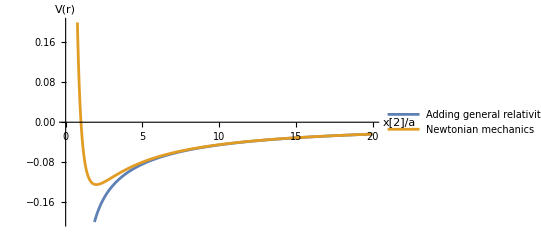
-Graphics-V[r]:Effective potential L=1

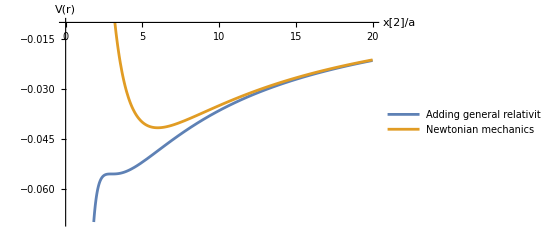
-Graphics-V[r]:Effective potential L=Sqrt[3]

2.12132

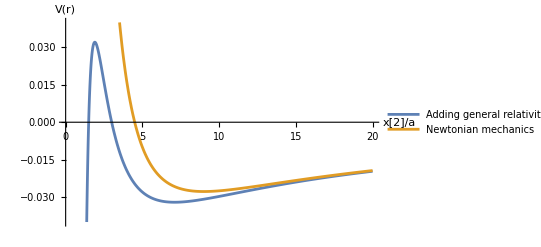
-Graphics-V[r]:Effective potential L=Sqrt[4.5]

2.5

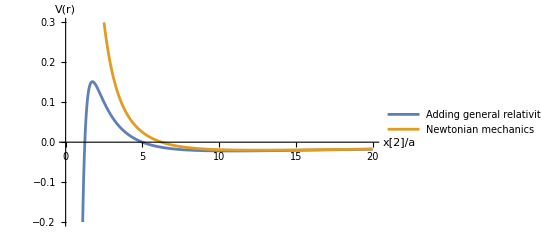
-Graphics-V[r]:Effective potential L=2.5

```mathematica
Remove["Global`*"]
Vr[r_]:=-L^2/(2 r^3)+L^2/(2 r^2)-1/(2 r)
Vn[r_]:=L^2/(2 r^2)-1/(2 r)
L=1;
g1=Plot[{Vr[r],Vn[r]},{r,0,20},PlotRange->{{0,20},{-.2,0.2}},PlotLegends->LineLegend[{"Adding general relativity","Newtonian mechanics"}],AxesLabel->{"x[2]/a",V[r]}];
Labeled[g1,"V[r]:Effective potential L=1",Top]
L=Sqrt[3];
g1=Plot[{Vr[r],Vn[r]},{r,0,20},PlotRange->{{0,20},{-.07,-0.01}},PlotLegends->LineLegend[{"Adding general relativity","Newtonian mechanics"}],AxesLabel->{"x[2]/a",V[r]}];
Labeled[g1,"V[r]:Effective potential L=Sqrt[3]",Top]
L=Sqrt[4.5]
g1=Plot[{Vr[r],Vn[r]},{r,0,20},PlotRange->{{0,20},{-.04,0.04}},PlotLegends->LineLegend[{"Adding general relativity","Newtonian mechanics"}],AxesLabel->{"x[2]/a",V[r]}];
Labeled[g1,"V[r]:Effective potential L=Sqrt[4.5]",Top]
L=2.5
g1=Plot[{Vr[r],Vn[r]},{r,0,20},PlotRange->{{0,20},{-.2,0.3}},PlotLegends->LineLegend[{"Adding general relativity","Newtonian mechanics"}],AxesLabel->{"x[2]/a",V[r]}];
Labeled[g1,"V[r]:Effective potential L=2.5",Top]
```

### 古典力学における惑星の運動を解いておこう。ニュートンの重力場中の質点の運動方程式は次のようである（この囲み内だけ、ドットはt の微分とする）。(7.21)

```mathematica
Remove["Global`*"]
"(7.21)"
𝕣̈==-G M 𝕣/r^3==-a c^2/2 𝕣/r^3
```

(7.21)

𝕣̈==-(G M 𝕣)/(r)^3==-(a (c)^2 𝕣)/(2 (r)^3)

### 一方、二次元極座標系ではr = r er であるが、単位ベクトルer やeϕ（この章では、基底ではなく長さ1 のベクトルとする）が運動と共に動くため、若干やっかいである。

```mathematica
Tensor[e,{r},{Void}]==Cos[ϕ]Tensor[e,{x},{Void}]+Sin[ϕ]Tensor[e,{y},{Void}]
Tensor[e,{ϕ},{Void}]==-Sin[ϕ]Tensor[e,{x},{Void}]+Cos[ϕ]Tensor[e,{y},{Void}]
```

e_r^==Cos[ϕ] e_x^+Sin[ϕ] e_y^

e_ϕ^==-Sin[ϕ] e_x^+Cos[ϕ] e_y^

### したがって、次式が得られる。

```mathematica
Tensor[ė,{r},{Void}]==IndexDerivative[Cos[ϕ]Tensor[e,{x},{Void}]+Sin[ϕ]Tensor[e,{y},{Void}],t]
%/.IndexDerivative[Tensor[e,{x_},{Void}],t]->0
Tensor[ė,{r},{Void}]==Tensor[e,{ϕ},{Void}]IndexDerivative[ϕ,t]
r1=IndexDerivative[Tensor[e,{r},{Void}],t]->Tensor[e,{ϕ},{Void}]IndexDerivative[ϕ,t]

Tensor[ė,{ϕ},{Void}]==IndexDerivative[-Sin[ϕ]Tensor[e,{x},{Void}]+Cos[ϕ]Tensor[e,{y},{Void}],t]
%/.IndexDerivative[Tensor[e,{x_},{Void}],t]->0
Tensor[ė,{ϕ},{Void}]==-Tensor[e,{r},{Void}]IndexDerivative[ϕ,t]
r2=IndexDerivative[Tensor[e,{ϕ},{Void}],t]->-Tensor[e,{r},{Void}]IndexDerivative[ϕ,t]
```

(ė)_r^==Cos[ϕ] ∂_t e_x^+∂_t e_y^ Sin[ϕ]-∂_t ϕ Sin[ϕ] e_x^+Cos[ϕ] ∂_t ϕ e_y^

(ė)_r^==-∂_t ϕ Sin[ϕ] e_x^+Cos[ϕ] ∂_t ϕ e_y^

(ė)_r^==∂_t ϕ e_ϕ^

∂_t e_r^→∂_t ϕ e_ϕ^

(ė)_ϕ^==Cos[ϕ] ∂_t e_y^-∂_t e_x^ Sin[ϕ]-Cos[ϕ] ∂_t ϕ e_x^-∂_t ϕ Sin[ϕ] e_y^

(ė)_ϕ^==-Cos[ϕ] ∂_t ϕ e_x^-∂_t ϕ Sin[ϕ] e_y^

(ė)_ϕ^==-∂_t ϕ e_r^

∂_t e_ϕ^→-∂_t ϕ e_r^

### さらに次のようになる。

```mathematica
𝕣̇==IndexDerivative[r Tensor[e,{r},{Void}] ,t]
%/.r1
r3=𝕣̇->%[[2]]
𝕣̈==IndexDerivative[%[[2]],t]//Expand
%/.r1/.r2
%[[1]]==Factor[%[[2,1;;2]]]+Factor[%[[2,3;;4]]]
r4=𝕣̈->%[[2]]
```

𝕣̇==r ∂_t e_r^+∂_t r e_r^

𝕣̇==∂_t r e_r^+r ∂_t ϕ e_ϕ^

𝕣̇→∂_t r e_r^+r ∂_t ϕ e_ϕ^

𝕣̈==∂_t r ∂_t e_r^+r ∂_t ϕ ∂_t e_ϕ^+∂_(t,t) r e_r^+∂_t r ∂_t ϕ e_ϕ^+r ∂_(t,t) ϕ e_ϕ^

𝕣̈==-r (∂_t ϕ)^2 e_r^+∂_(t,t) r e_r^+2 ∂_t r ∂_t ϕ e_ϕ^+r ∂_(t,t) ϕ e_ϕ^

𝕣̈==-((r (∂_t ϕ)^2-∂_(t,t) r) e_r^)+(2 ∂_t r ∂_t ϕ+r ∂_(t,t) ϕ) e_ϕ^

𝕣̈→-((r (∂_t ϕ)^2-∂_(t,t) r) e_r^)+(2 ∂_t r ∂_t ϕ+r ∂_(t,t) ϕ) e_ϕ^

### これらを式(7.21) へ代入すると、

```mathematica
s4=(𝕣̈/.r4)==-a c^2/2 𝕣/r^3 /. 𝕣->r Tensor[e,{r},{Void}]
s5=Coefficient[%[[1]],Tensor[e,{r},{Void}]]==Coefficient[%[[2]],Tensor[e,{r},{Void}]]
s6=Coefficient[s4[[1]],Tensor[e,{ϕ},{Void}]]==Coefficient[s4[[2]],Tensor[e,{ϕ},{Void}]]
```

-((r (∂_t ϕ)^2-∂_(t,t) r) e_r^)+(2 ∂_t r ∂_t ϕ+r ∂_(t,t) ϕ) e_ϕ^==-(a (c)^2 e_r^)/(2 (r)^2)

-r (∂_t ϕ)^2+∂_(t,t) r==-(a (c)^2)/(2 (r)^2)

2 ∂_t r ∂_t ϕ+r ∂_(t,t) ϕ==0

### 後式は面積速度一定r^2ϕ̇= h になる。この結果を前式へ代入すると、次の運動方程式が得られる。(7.22)

```mathematica
r^2 IndexDerivative[ϕ[t],t]==h
s7=Solve[%,IndexDerivative[ϕ[t],t]]
s6=s5/.ϕ->ϕ[t]/.%[[1]]
"(7.22)"
```

(r)^2 ∂_t ϕ[t]==h

{{∂_t ϕ[t]→h/(r)^2}}

-(h)^2/(r)^3+∂_(t,t) r==-(a (c)^2)/(2 (r)^2)

(7.22)

### 軌道を計算するには、r(ϕ) を求める必要があるが、この際、u(ϕ) = 1/r(ϕ) として計算するのがよい。ダッシュ（′）をϕによる微分とすると、次のようになる。

```mathematica
ṙ==D[1/u[ϕ[t]],t]/.u[ϕ[t]]->1/r/.D[ϕ[t],t]->h/r^2
r̈==D[%[[2]],t]
s8=%/.D[ϕ[t],t]->h u[ϕ[t]]^2
```

ṙ==-h u'[ϕ[t]]

r̈==-h ϕ'[t] u''[ϕ[t]]

r̈==-(h)^2 (u[ϕ[t]])^2 u''[ϕ[t]]

### これらを式(7.22) へ代入すると、l = 2a(h/ac)^2 として、

```mathematica
s9=s6/.IndexDerivative[r,t,t]->s8[[2]]
l==2a(h/(a c))^2
Solve[%,a]
s9/.%[[1]]
%/.r->1/u[ϕ[t]]
s10=Simplify[-%[[1]]/(h^2u[ϕ[t]]^2)]==Simplify[-%[[2]]/(h^2u[ϕ[t]]^2)]
```

-(h)^2/(r)^3-(h)^2 (u[ϕ[t]])^2 u''[ϕ[t]]==-(a (c)^2)/(2 (r)^2)

l==(2 (h)^2)/(a (c)^2)

{{a→(2 (h)^2)/((c)^2 l)}}

-(h)^2/(r)^3-(h)^2 (u[ϕ[t]])^2 u''[ϕ[t]]==-(h)^2/(l (r)^2)

-(h)^2 (u[ϕ[t]])^3-(h)^2 (u[ϕ[t]])^2 u''[ϕ[t]]==-((h)^2 (u[ϕ[t]])^2)/l

u[ϕ[t]]+u''[ϕ[t]]==(l)^-1

### というほとんど単振動の式と同じ式が得られる。この解は単振動に一定項のついた次式となる

```mathematica
DSolve[s10,u[ϕ[t]],ϕ[t]]
u[ϕ[t]]/.%[[1]]
u==(1+ϵ Cos[ϕ-ϕ0])/l
```

{{u[ϕ[t]]→(l)^-1+C[1] Cos[ϕ[t]]+C[2] Sin[ϕ[t]]}}

(l)^-1+C[1] Cos[ϕ[t]]+C[2] Sin[ϕ[t]]

u==(1+ϵ Cos[ϕ-ϕ0])/l

### これより、最終の軌跡として次式が得られる。

```mathematica
r==1/%[[2]]
```

r==l/(1+ϵ Cos[ϕ-ϕ0])

### これは太陽の位置を焦点の片方とする楕円（または放物線、双曲線）の式である。これよりlは軌道の平均半径（厳密にはu の平均値の逆数）であることがわかる。また、u を得た際の振幅の任意性を示すε は、これら二次曲線の離心率（orbital eccentricity）であり、0 ≤ ε ≤ 1で楕円、1 で放物線、1 以上で双曲線となる。式 (7.22) に r’を掛けて積分すると、有効ポテンシャル法に持ち込むことができる。右辺の定数は、式(7.23) を使って決定している。

```mathematica
s10=h^2/(2r[ϕ]^2)-a c^2/(2r[ϕ])+1/2  D[r[ϕ],ϕ]^2==c^2/8 (a c/h)^2(ϵ^2-1)
D[%[[1]],ϕ]==0
Simplify[%[[1]]/D[r[ϕ],ϕ]]==0
"(7.22)"
```

(h)^2/(2 (r[ϕ])^2)-(a (c)^2)/(2 r[ϕ])+1/2 (r'[ϕ])^2==((a)^2 (c)^4 (-1+(ϵ)^2))/(8 (h)^2)

-((h)^2 r'[ϕ])/(r[ϕ])^3+(a (c)^2 r'[ϕ])/(2 (r[ϕ])^2)+r'[ϕ] r''[ϕ]==0

-(h)^2/(r[ϕ])^3+(a (c)^2)/(2 (r[ϕ])^2)+r''[ϕ]==0

(7.22)

```mathematica
s10[[1]]
%/.r[ϕ]->l/(1+ϵ Cos[ϕ-ϕ0])/.r'[ϕ]->-h  D[(1+ϵ Cos[ϕ-ϕ0])/l,ϕ]
s11=Expand[%]
Factor[s11[[5;;6]]]/.Sin[a_]^2+Cos[a_]^2->1
%+Factor[s11[[3;;4]]]+s11[[1;;2]]/.l->2 a(h/(a c))^2
Simplify[%]
```

(h)^2/(2 (r[ϕ])^2)-(a (c)^2)/(2 r[ϕ])+1/2 (r'[ϕ])^2

-(a (c)^2 (1+ϵ Cos[ϕ-ϕ0]))/(2 l)+((h)^2 (1+ϵ Cos[ϕ-ϕ0])^2)/(2 (l)^2)+((h)^2 (ϵ)^2 (Sin[ϕ-ϕ0])^2)/(2 (l)^2)

(h)^2/(2 (l)^2)-(a (c)^2)/(2 l)+((h)^2 ϵ Cos[ϕ-ϕ0])/(l)^2-(a (c)^2 ϵ Cos[ϕ-ϕ0])/(2 l)+((h)^2 (ϵ)^2 (Cos[ϕ-ϕ0])^2)/(2 (l)^2)+((h)^2 (ϵ)^2 (Sin[ϕ-ϕ0])^2)/(2 (l)^2)

((h)^2 (ϵ)^2)/(2 (l)^2)

-((a)^2 (c)^4)/(8 (h)^2)+((a)^2 (c)^4 (ϵ)^2)/(8 (h)^2)

((a)^2 (c)^4 (-1+(ϵ)^2))/(8 (h)^2)

### 有効ポテンシャル法の相対論的式(7.20) と惑星の有効ポテンシャル法の式(7.24) を比較してみると、右辺が異なるが、これらは共に任意定数なので等しいとすることができる。さらにV の中にr−3 の比例項が入っているが、これこそ正に相対論的効果である。この項はr の大きさがl の程度であるとすると、他の二項と比較し、a/l の程度、つまり（重力半径/軌道サイズ）である。これが1 に比べ十分小さいという条件で検討を行う。この効果が軌道にどのような影響を与えるかであるが、太陽にもっとも近い水星の楕円軌道全体の長径方向が徐々に（前進）移動していくことが知られている。天文学的には楕円軌道でもっとも太陽に近い近日点移動（perihelion shift）という形で知られている。他の惑星からの摂動などの影響を取り去っても、さらに僅かに残る移動があるのである。アインシュタインはこの値を予測することで、一般相対性理論の最初の証としたのである。 相対論の効果はごく僅かなので、そこにおける軌道はほぼ式(7.23) の形で与えられるとする。解析に便利なu で表わすと次式である。

```mathematica
Remove["Global`*"]
u[t]=(1+e Cos[P ϕ[t]])/L
r[t]=1/u[t]
```

(1+e Cos[P ϕ[t]])/L

L/(1+e Cos[P ϕ[t]])

### ϕ0 は座標をうまく選んだということで除去しているが、L、e、P は振幅l、離心率ε、1 から の微小なずれを含んでいる。

```mathematica
s1=D[r[t],t]
%/. 1+e Cos[P ϕ[t]]->L/r[t]
%/.ϕ'[t]->h/r[t]^2
s2=ṙ[t]^2/2==%^2/2 /.Sin[P ϕ[t]]^2->1-Cos[P ϕ[t]]^2
```

(e L P Sin[P ϕ[t]] ϕ'[t])/(1+e Cos[P ϕ[t]])^2

(e L P Sin[P ϕ[t]] ϕ'[t])/(1+e Cos[P ϕ[t]])^2

(e h P Sin[P ϕ[t]])/L

1/2 (ṙ[t])^2==((e)^2 (h)^2 (P)^2 (1-(Cos[P ϕ[t]])^2))/(2 (L)^2)

### これらを式(7.20) に代入すると次のようになる。

```mathematica
"(7.20)"
1/2(-a h^2/r^3+h^2/r^2-a c^2/r)+1/2 IndexDerivative[r,τ]^2
"光速に比べて十分低速の粒子を対象にするので"
dτ≃dt
1/2(-a h^2/r^3+h^2/r^2-a c^2/r)+1/2 IndexDerivative[r,t]^2
s4=%/.%[[2]]->s2[[2]]/.r->r[t]
```

(7.20)

1/2 (-(a (h)^2)/(r)^3+(h)^2/(r)^2-(a (c)^2)/r)+1/2 (∂_τ r)^2

光速に比べて十分低速の粒子を対象にするので

dτ≃dt

1/2 (-(a (h)^2)/(r)^3+(h)^2/(r)^2-(a (c)^2)/r)+1/2 (∂_t r)^2

((e)^2 (h)^2 (P)^2 (1-(Cos[P ϕ[t]])^2))/(2 (L)^2)+1/2 (-(a (c)^2 (1+e Cos[P ϕ[t]]))/L+((h)^2 (1+e Cos[P ϕ[t]])^2)/(L)^2-(a (h)^2 (1+e Cos[P ϕ[t]])^3)/(L)^3)

### 離心率e は円軌道に近いため、ほぼ0 であるため、e^3 の項は無視した。この式のcos の冪乗の係数比較の式を連立させると、L、e、P が容易に得られ、いずれにも(ac/h)2 に比例する微小なずれが現われるが、特にP に着目すると、cos の2 次の係数の比較が重要となる。

```mathematica
Expand[s4]/.e^3->0
s5=CoefficientList[%,Cos[P ϕ[t]]]
s6=s5[[1]]==(a c^2)^2(ϵ^2-1)/(8 h^2)
s7=s5[[2]]==0
s8=s5[[3]]==0
```

-(a (h)^2)/(2 (L)^3)+(h)^2/(2 (L)^2)-(a (c)^2)/(2 L)+((e)^2 (h)^2 (P)^2)/(2 (L)^2)-(3 a e (h)^2 Cos[P ϕ[t]])/(2 (L)^3)+(e (h)^2 Cos[P ϕ[t]])/(L)^2-(a (c)^2 e Cos[P ϕ[t]])/(2 L)-(3 a (e)^2 (h)^2 (Cos[P ϕ[t]])^2)/(2 (L)^3)+((e)^2 (h)^2 (Cos[P ϕ[t]])^2)/(2 (L)^2)-((e)^2 (h)^2 (P)^2 (Cos[P ϕ[t]])^2)/(2 (L)^2)

{-(a (h)^2)/(2 (L)^3)+(h)^2/(2 (L)^2)-(a (c)^2)/(2 L)+((e)^2 (h)^2 (P)^2)/(2 (L)^2),-(3 a e (h)^2)/(2 (L)^3)+(e (h)^2)/(L)^2-(a (c)^2 e)/(2 L),-(3 a (e)^2 (h)^2)/(2 (L)^3)+((e)^2 (h)^2)/(2 (L)^2)-((e)^2 (h)^2 (P)^2)/(2 (L)^2)}

-(a (h)^2)/(2 (L)^3)+(h)^2/(2 (L)^2)-(a (c)^2)/(2 L)+((e)^2 (h)^2 (P)^2)/(2 (L)^2)==((a)^2 (c)^4 (-1+(ϵ)^2))/(8 (h)^2)

-(3 a e (h)^2)/(2 (L)^3)+(e (h)^2)/(L)^2-(a (c)^2 e)/(2 L)==0

-(3 a (e)^2 (h)^2)/(2 (L)^3)+((e)^2 (h)^2)/(2 (L)^2)-((e)^2 (h)^2 (P)^2)/(2 (L)^2)==0

### これより、L ≑l として得られるP は

```mathematica
s9=Solve[{s8},{P}]/.L->l
```

{{P→-(-3 a+l)^(1/2)/(l)^(1/2)},{P→(-3 a+l)^(1/2)/(l)^(1/2)}}

### となる。軌道の近日点は、Pϕ= 2π となるごとに発生するので、ϕは2π ではなく、次の角度だけ回ることになる。

```mathematica
P ϕ==2 Pi
Solve[%,ϕ]
ϕ/.%[[1]]/.s9[[2]]
%/. 1/(-3a+l)^(1/2)->l^(-1/2)(1+3/2a/l)
%[[2,2]] 2 Pi
%/.a->2953/.l->0.3871*149598700000
%/(2 Pi)*360*60*60*415
%/(1-0.20563^2)
```

P ϕ==2 π

{{ϕ→(2 π)/P}}

(2 (l)^(1/2) π)/(-3 a+l)^(1/2)

2 (1+(3 a)/(2 l)) π

(3 a π)/l

4.806×10^-7

41.1393

42.9556

### ちなみに、太陽の相対論的効果をもっとも受けやすい水星ですら、43 秒/100 年というごく小さな値である。最近の観測結果はこの値の±1% 以内であり、この一致から一般相対性理論の信頼性が格段に上がったのである。

### 100年で水星は415周公転する。2πラジアンは,360 × 60 × 60 秒だから,

### -Graphics-

```mathematica
"100年で42.95秒角"
360 *3600*3/2*2953/(1-0.2056^2)/(149598700000*0.3871)415
% /(360 60 60)*365*24*60
"100年で17.402分　時間"
%%*60/100
"1年で10.4524秒　時間"
%%*0.241
"水星公転１周で2.519秒　"
```

100年で42.95秒角

42.9551

17.4207

100年で17.402分　時間

10.4524

1年で10.4524秒　時間

2.51903

水星公転１周で2.519秒

#### Planetary motion in classical mechanics ϵ:Orbital eccentricity ϕ0:Initial Phase

```mathematica
Remove["Global`*"]
Manipulate[
s1=PolarPlot[{1/(1+ϵ Cos[ϕ-ϕ0])},{ϕ,0,2Pi},PlotRange->{{-6.2,6.2},{-6.2,6.2}},ColorFunction->Function[{x,y},Red]];
s2=Plot[{Tan[ϕ0]x },{x,-6.2,6.2},PlotRange->{{-6.2,6.2},{-6.2,6.2}},ColorFunction->Function[{x,y},Green]];
R1=(-1/(1-ϵ )+1/(1+ϵ ))/2;
s3=Plot[{-1/Tan[ϕ0](x-R1 Cos[ϕ0])+R1  Sin[ϕ0] },{x,-6.2,6.2},PlotRange->{{-6.2,6.2},{-6.2,6.2}},ColorFunction->Function[{x,y},Blue]];
Show[s1,s2,s3]
,{ϵ,0,1-0.001},{ϕ0,-Pi+0.0001,Pi}
]
```

#### Planetary motion in general relativity. ϵ=0.75:Orbital eccentricity Pp=3 a /l l=2 a (h/(a c)^2 Schwarzschild radius:a=2 G M/c^2 Area Velocity:h

```mathematica
Manipulate[
s1=PolarPlot[{1/(1+0.75 Cos[Sqrt[(1-Pp)] (ϕ-ϕ0)])},{ϕ,0,20Pi},PlotRange->{{-4.2,4.2},{-4.2,4.2}},ColorFunction->Function[{x,y,ϕ},Hue[ϕ]]];

Show[s1]
,{ϕ0,-Pi,Pi},{Pp,0 ,.1}
]
```

## 7.4.3 重力場における光の測地線

### アインシュタインの考えた等価原理にしたがうと、光線も重力下では落下し、光の湾曲（light bending）が現われるはずである。光線の軌跡を解く際、ほとんどの作業は質点の軌跡と同じである。ただし、ds = 0 なので、s の替りに媒介変数σ を利用する必要がある。したがって、前出の測地線の方程式 (7.12) から式 (7.15) のṙなどの微分はすべて σ による微分とする必要がある。また、r に関する測地線を求める際に利用した式(7.18) は、左辺をc2 → 0としてから、全体をdσ2 で割る。ṫ およびϕ̇には、式(7.16) および式(7.17) は成立するので、次式に見られるように、式(7.20) のV の括弧内から−1/r が消えることと、右辺が変る以外はすべて同じ形になる。(7.25)

```mathematica
Remove["Global`*"]
ClearAttributes[Times,Orderless]
"(7.11)"
-ds^2==(c dτ)^2==(1-a/r)dct^2-(1-a/r)^-1 dr^2-r^2dθ^2-r^2Sin[θ]^2dϕ^2
SetAttributes[Times,Orderless]
"両辺をdτで割り、シュバルツシルト計量空間での測地線条件を代入すると"
"(7.18)"
s1=c^2==c^2K^2(1-a/r)^-1-(1-a/r)^-1 IndexDerivative[r,τ]^2-(h/r)^2==0
"光は光速なのでds=0となるので、左辺のc^2を０とする。"
"(7.20)"
Simplify[(1-a/r)s1[[2]]]==0
Expand[%]
s2=-%[[1,2;;3]]/2-%[[1,4]]/2==%[[1,1]]/2/.τ->σ

"(7.25)"
```

(7.11)

-(ds)^2==(c)^2 (dτ)^2==(1-a/r) (dct)^2-(dr)^2/(1-a/r)-(r)^2 (dθ)^2-(r)^2 (Sin[θ])^2 (dϕ)^2

両辺をdτで割り、シュバルツシルト計量空間での測地線条件を代入すると

(7.18)

(c)^2==((c)^2 (K)^2)/(1-a/r)-(h)^2/(r)^2-(∂_τ r)^2/(1-a/r)==0

光は光速なのでds=0となるので、左辺のc^2を０とする。

(7.20)

(c)^2 (K)^2+((h)^2 (a-r))/(r)^3-(∂_τ r)^2==0

(c)^2 (K)^2+(a (h)^2)/(r)^3-(h)^2/(r)^2-(∂_τ r)^2==0

1/2 (-(a (h)^2)/(r)^3+(h)^2/(r)^2)+1/2 (∂_σ r)^2==1/2 (c)^2 (K)^2

(7.25)

### V の括弧内第二項の相対論的効果がない場合の軌道は、次式で与えられる。

```mathematica
r==R/(Cos[ϕ-ϕ0])
```

r==R Sec[ϕ-ϕ0]

```mathematica
s2/.IndexDerivative[r,σ]->-h  IndexDerivative[1/r,ϕ]
%/.r->R/Cos[ϕ-ϕ0]
%/.R->h/(c K)
%/.IndexDerivative[ϕ0,ϕ]->0/.IndexDerivative[ϕ,ϕ]->1/.IndexDerivative[c,ϕ]->0/.IndexDerivative[1/h,ϕ]->0
%/.IndexDerivative[K,ϕ]->0
Expand[%]
Factor[%[[1,{1,3}]]]+%[[1,2]]==%[[2]]
%/.Sin[x_]^2+Cos[x_]^2->1
Simplify[%]
```

1/2 (-(a (h)^2)/(r)^3+(h)^2/(r)^2)+1/2 (h)^2 (∂_ϕ (r)^-1)^2==1/2 (c)^2 (K)^2

1/2 (((h)^2 (Cos[ϕ-ϕ0])^2)/(R)^2-(a (h)^2 (Cos[ϕ-ϕ0])^3)/(R)^3)+1/2 (h)^2 (Cos[ϕ-ϕ0] ∂_ϕ (R)^-1-((∂_ϕ ϕ-∂_ϕ ϕ0) Sin[ϕ-ϕ0])/R)^2==1/2 (c)^2 (K)^2

1/2 ((c)^2 (K)^2 (Cos[ϕ-ϕ0])^2-(a (c)^3 (K)^3 (Cos[ϕ-ϕ0])^3)/h)+1/2 (h)^2 (Cos[ϕ-ϕ0] ((K ∂_ϕ c)/h+c (K ∂_ϕ (h)^-1+(∂_ϕ K)/h))-(c K (∂_ϕ ϕ-∂_ϕ ϕ0) Sin[ϕ-ϕ0])/h)^2==1/2 (c)^2 (K)^2

1/2 ((c)^2 (K)^2 (Cos[ϕ-ϕ0])^2-(a (c)^3 (K)^3 (Cos[ϕ-ϕ0])^3)/h)+1/2 (h)^2 ((c Cos[ϕ-ϕ0] ∂_ϕ K)/h-(c K Sin[ϕ-ϕ0])/h)^2==1/2 (c)^2 (K)^2

1/2 ((c)^2 (K)^2 (Cos[ϕ-ϕ0])^2-(a (c)^3 (K)^3 (Cos[ϕ-ϕ0])^3)/h)+1/2 (c)^2 (K)^2 (Sin[ϕ-ϕ0])^2==1/2 (c)^2 (K)^2

1/2 (c)^2 (K)^2 (Cos[ϕ-ϕ0])^2-(a (c)^3 (K)^3 (Cos[ϕ-ϕ0])^3)/(2 h)+1/2 (c)^2 (K)^2 (Sin[ϕ-ϕ0])^2==1/2 (c)^2 (K)^2

-(a (c)^3 (K)^3 (Cos[ϕ-ϕ0])^3)/(2 h)+1/2 (c)^2 (K)^2 ((Cos[ϕ-ϕ0])^2+(Sin[ϕ-ϕ0])^2)==1/2 (c)^2 (K)^2

1/2 (c)^2 (K)^2-(a (c)^3 (K)^3 (Cos[ϕ-ϕ0])^3)/(2 h)==1/2 (c)^2 (K)^2

(a c K Cos[ϕ-ϕ0])/h==0

### ただし、R = h/cK である。これが正しいことは、ṙ= −hu’= −h(1/r)’ を利用して、この式を式(7.25) に代入することで確かめられる。また、この式は直線を極座標系で表示したものになっている。相対論的補正が入った場合には、次のような解を仮定する。

```mathematica
r==R/(f[ϕ]+Cos[ϕ])
s2/.IndexDerivative[r,σ]->-r  IndexDerivative[1/r,ϕ]
%/.r->R/(f[ϕ]+Cos[ϕ])
%/.IndexDerivative[R^-1,ϕ]->0
%/.IndexDerivative[Cos[ϕ],ϕ]->Sin[ϕ]
%/.R->h/(c K)
Expand[%[[1]]]==%[[2]]
%/.f[ϕ]^2->0
%/.f[ϕ]^3->0
```

r==R/(Cos[ϕ]+f[ϕ])

1/2 (-(a (h)^2)/(r)^3+(h)^2/(r)^2)+1/2 (r)^2 (∂_ϕ (r)^-1)^2==1/2 (c)^2 (K)^2

1/2 (((h)^2 (Cos[ϕ]+f[ϕ])^2)/(R)^2-(a (h)^2 (Cos[ϕ]+f[ϕ])^3)/(R)^3)+((R)^2 ((Cos[ϕ]+f[ϕ]) ∂_ϕ (R)^-1+(∂_ϕ Cos[ϕ]+∂_ϕ f[ϕ])/R)^2)/(2 (Cos[ϕ]+f[ϕ])^2)==1/2 (c)^2 (K)^2

1/2 (((h)^2 (Cos[ϕ]+f[ϕ])^2)/(R)^2-(a (h)^2 (Cos[ϕ]+f[ϕ])^3)/(R)^3)+(∂_ϕ Cos[ϕ]+∂_ϕ f[ϕ])^2/(2 (Cos[ϕ]+f[ϕ])^2)==1/2 (c)^2 (K)^2

1/2 (((h)^2 (Cos[ϕ]+f[ϕ])^2)/(R)^2-(a (h)^2 (Cos[ϕ]+f[ϕ])^3)/(R)^3)+(∂_ϕ f[ϕ]+Sin[ϕ])^2/(2 (Cos[ϕ]+f[ϕ])^2)==1/2 (c)^2 (K)^2

1/2 ((c)^2 (K)^2 (Cos[ϕ]+f[ϕ])^2-(a (c)^3 (K)^3 (Cos[ϕ]+f[ϕ])^3)/h)+(∂_ϕ f[ϕ]+Sin[ϕ])^2/(2 (Cos[ϕ]+f[ϕ])^2)==1/2 (c)^2 (K)^2

1/2 (c)^2 (K)^2 (Cos[ϕ])^2-(a (c)^3 (K)^3 (Cos[ϕ])^3)/(2 h)+(c)^2 (K)^2 Cos[ϕ] f[ϕ]-(3 a (c)^3 (K)^3 (Cos[ϕ])^2 f[ϕ])/(2 h)+1/2 (c)^2 (K)^2 (f[ϕ])^2-(3 a (c)^3 (K)^3 Cos[ϕ] (f[ϕ])^2)/(2 h)-(a (c)^3 (K)^3 (f[ϕ])^3)/(2 h)+(∂_ϕ f[ϕ])^2/(2 (Cos[ϕ]+f[ϕ])^2)+(∂_ϕ f[ϕ] Sin[ϕ])/(Cos[ϕ]+f[ϕ])^2+(Sin[ϕ])^2/(2 (Cos[ϕ]+f[ϕ])^2)==1/2 (c)^2 (K)^2

1/2 (c)^2 (K)^2 (Cos[ϕ])^2-(a (c)^3 (K)^3 (Cos[ϕ])^3)/(2 h)+(c)^2 (K)^2 Cos[ϕ] f[ϕ]-(3 a (c)^3 (K)^3 (Cos[ϕ])^2 f[ϕ])/(2 h)-(a (c)^3 (K)^3 (f[ϕ])^3)/(2 h)+(∂_ϕ f[ϕ])^2/(2 (Cos[ϕ]+f[ϕ])^2)+(∂_ϕ f[ϕ] Sin[ϕ])/(Cos[ϕ]+f[ϕ])^2+(Sin[ϕ])^2/(2 (Cos[ϕ]+f[ϕ])^2)==1/2 (c)^2 (K)^2

1/2 (c)^2 (K)^2 (Cos[ϕ])^2-(a (c)^3 (K)^3 (Cos[ϕ])^3)/(2 h)+(c)^2 (K)^2 Cos[ϕ] f[ϕ]-(3 a (c)^3 (K)^3 (Cos[ϕ])^2 f[ϕ])/(2 h)+(∂_ϕ f[ϕ])^2/(2 (Cos[ϕ]+f[ϕ])^2)+(∂_ϕ f[ϕ] Sin[ϕ])/(Cos[ϕ]+f[ϕ])^2+(Sin[ϕ])^2/(2 (Cos[ϕ]+f[ϕ])^2)==1/2 (c)^2 (K)^2

### ここでも、ϕ0 は、座標をうまく選んだということで除去している。これを代入すると、次の微分方程式が得られるが、これは定数変化法で解くことができる。

```mathematica
s3=f[ϕ]Cos[ϕ]-D[f[ϕ],ϕ]Sin[ϕ]==a/(2 R) Cos[ϕ]^3
```

Cos[ϕ] f[ϕ]-Sin[ϕ] f'[ϕ]==(a (Cos[ϕ])^3)/(2 R)

### ただし、f の二乗等、微小量は無視した。

```mathematica
DSolve[s3,f[ϕ],ϕ]
f[ϕ]/.%[[1]]/.C[1]->A
s4=TrigReduce[Expand[%]]//Expand
```

{{f[ϕ]→C[1] Sin[ϕ]-(a (-Csc[ϕ]-Sin[ϕ]) Sin[ϕ])/(2 R)}}

A Sin[ϕ]-(a (-Csc[ϕ]-Sin[ϕ]) Sin[ϕ])/(2 R)

(3 a)/(4 R)-(a Cos[2 ϕ])/(4 R)+A Sin[ϕ]

### 一般性を損なうことなくA = 0 とすることができるので、相対論的光の軌道は次のようになる。

```mathematica
s5=f[ϕ]->(s4/.A->0)
r==R/(f[ϕ]+Cos[ϕ])/.s5
Simplify[%]
```

f[ϕ]→(3 a)/(4 R)-(a Cos[2 ϕ])/(4 R)

r==R/((3 a)/(4 R)+Cos[ϕ]-(a Cos[2 ϕ])/(4 R))

r==(4 (R)^2)/(4 R Cos[ϕ]-a (-3+Cos[2 ϕ]))

### r が無限大になるところでのϕを求めると、光の湾曲は2a/R であることが導かれる。太陽表面をすれすれに通過する恒星の位置ずれを想定する場合、1.74 秒となることが導かれる。観測結果は±15% 程度の誤差範囲で予測に一致している。

```mathematica
Remove["Global`*"]
Manipulate[
s1=PolarPlot[{4 R^2/(4 R Abs[Cos[ϕ]]+3-1 Cos[2 ϕ] ),1},{ϕ,-Pi,Pi },PlotRange->{{-5,5},{-5,5}}];
Show[s1],{R,1.4,5}
]
```

## 7.4.4 重力赤方偏移

### 重力ポテンシャルの大きなところで発射された光を重力ポテンシャルの小さいところで観測すると、周波数が低く見えることを、重力赤方偏移（gravitational redshift）という。これは、空間に固定された二点間の間の時間間隔に対して

```mathematica
dcτ^2==Tensor[g,{0,0},{Void,Void}]dct^2
√Tensor[g,{0,0},{Void,Void}]
```

(dcτ)^2==(dct)^2 g_00^

(g_00^)^(1/2)

### が成立するため("("g_00^(" "" ")")")^(1/2) の影響を受けることによる。重力ポテンシャルの大きなところで発射されたパルス間隔dt に対するdτ は("("g_00^(" "" ")")")^(1/2) が小さい分、短くなる。時間間隔は固有時間で観測されるため、このdτ の差が周波数の差を与える。この他にもいくつかの一般相対性原理に基づく効果があるが、詳細は天文学や一般相対性理論に特化した書など*1を参考にしてほしい。

### *1 例えば、窪田高弘、佐々木隆「相対性理論」裳華房テキストシリーズ-物理学（2001）など

## 7.4.5 ブラックホール

### 重力半径a では、 g_00^(" "" ")= 1 −a/r = 0 となり、時計が無限に遅れることになり、どんな物体も光ですら、そこへ到達したりそこから外へ脱出するには無限の時間がかかることになる。そこで、この半径以下のサイズを持つ星はブラックホール（black hole）と呼ばれる。一方で、図7.1 のところで述べたように、十分高いE を有する粒子は、中心に向って落下していくが、r = a に逹したときにも有限の速度 ṙ（四元速度の第 1 成分）を持って突入していくのである。ということで、重力半径a で何が起るのかをやや詳細に検討してみよう。特に関心が高いのは、重力半径付近における質点の速度である。議論を簡単にするために、h = 0 の直線運動を仮定しよう。式(7.19) から直ちに次式が得られる。

```mathematica
ṙ==±Sqrt[c^2(K^2-1)+a c^2/r-h^2/r^2+a h^2/r^3]
s1=%/.h->0
s3=|%[[1]]/c|==|dr/dct|==±Sqrt[-1+K^2+a/r]
s1/.r->r0
%[[2,1]]==0
s2=Solve[%,K]
```

ṙ==±((c)^2 (-1+(K)^2)+(a (h)^2)/(r)^3-(h)^2/(r)^2+(a (c)^2)/r)^(1/2)

ṙ==±((c)^2 (-1+(K)^2)+(a (c)^2)/r)^(1/2)

|(ṙ)/c|==|dr/dct|==±(-1+(K)^2+a/r)^(1/2)

OverDot[r0]==±((c)^2 (-1+(K)^2)+(a (c)^2)/r0)^(1/2)

((c)^2 (-1+(K)^2)+(a (c)^2)/r0)^(1/2)==0

{{K→-(-a+r0)^(1/2)/(r0)^(1/2)},{K→(-a+r0)^(1/2)/(r0)^(1/2)}}

### ṙ は落下時に負、打上げ時に正となる。r = r0 で ṙ= 0 だったとすると、K =Sqrt[1 −a/r0] である。この場合、上式は次のように書ける。

```mathematica
s3/.s2[[1]]
s4=Simplify[%[[3,1]]]
```

|(ṙ)/c|==|dr/dct|==±(-1+a/r+(-a+r0)/r0)^(1/2)

(a ((r)^-1-(r0)^-1))^(1/2)

### -Graphics-

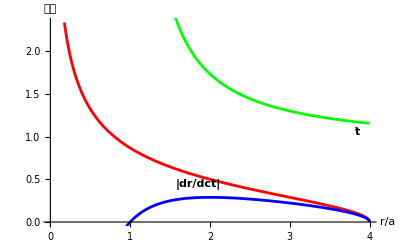

```mathematica
Remove["Global`*"]
r0=4;
g1=Plot[{Sqrt[1/r-1/r0]},{r,0,4},ColorFunction->Function[{x,y},Red],PlotLabels->Placed[{"|ṙ|/c"},Above],AxesLabel->{"r/a","速度"},LabelStyle->Directive[Medium,Black,Bold]];
g2=Plot[{Sqrt[1-1/r0]/(1-1/r)},{r,1,4},ColorFunction->Function[{x,y},Green],PlotLabels->Placed[{"ṫ"},Below],LabelStyle->Directive[Medium,Black,Bold]];
g3=Plot[{(1-1/r)Sqrt[1/r-1/r0]/Sqrt[1-1/r0]},{r,0,4},ColorFunction->Function[{x,y},Blue],PlotLabels->Placed["|dr/dct|                         ",Above],LabelStyle->Directive[Medium,Black,Bold]];
Show[g1,g2,g3]
```

### 一方、式(7.16) のK を置き換えると、直ちに次式が得られる。

```mathematica
"(7.16)"
(1-a/r)ṫ==K
%/.s2[[1]]
s5=Solve[%,ṫ]
```

(7.16)

(1-a/r) ṫ==K

(1-a/r) ṫ==-(-a+r0)^(1/2)/(r0)^(1/2)

{{ṫ→(r (-a+r0)^(1/2))/((a-r) (r0)^(1/2))}}

### これらの結果を図 7.2 に示す。|ṙ| を見ると、任意の点 r0 から r ≥ 0 の任意の点まで、有限の固有時間で到達できることがわかる。しかし、g00 およびg11 の符号が変るという大事件の起るr = a を質点が何の影響も感じず連続的に通過するのはむしろおかしいような気がする。 一方、ṫ はr = a で無限大になる。古典的速度であるこれら二つの比|dr/dt| は次式で与えられる。

```mathematica
|dr/dct|==|dr/dcτ|/|dt/dτ|
|dr/dct|==ṙ/c/ṫ
%/.s5[[1]]/.ṙ/c->s4
Simplify[%]
```

|dr/dct|==(|dr/dcτ|)/(|dt/dτ|)

|dr/dct|==(ṙ)/(c ṫ)

|dr/dct|==((a-r) (a ((r)^-1-(r0)^-1))^(1/2) (r0)^(1/2))/(r (-a+r0)^(1/2))

|dr/dct|==((a-r) (a ((r)^-1-(r0)^-1))^(1/2) (r0)^(1/2))/(r (-a+r0)^(1/2))

### その結果も同図に示すが、r = a に近寄るにつれて減少していき、運動は重力半径で停止するかに見える。これ故に、どんな物質でも重力半径に補足されてしまうという理解が広まっている。ここで一つ疑問がある。この現象を観測している人に対し、時間はt で経過していくのであろうか。改めて、r やt がどういう役割を演ずるために導入されたかを考えてみよう。これらの座標系は、質点の運動が測地線になるように導入された座標系であり、実際の寸法に裏打ちされた座標系ではないのである。例えば、二次元極座標系で、ある半径における円周を計算するには、dϕの積分では駄目で、r dϕを用いて計算しなければならない。同様に、シュバルツシルト計量で、実際の寸法を議論するには、r 方向にはdR = dr/p1 −a/r、ct 方向にはdcT = dctp1 −a/r を用いて計算すべきではないだろうか。 そこで、これらの固有時間（距離）で補正された速度を計算してみると次のようになる。

### -Graphics-

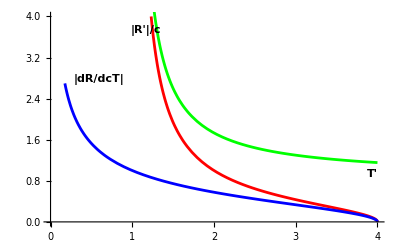

```mathematica
Remove["Global`*"]
r0=4;
g1=Plot[{Sqrt[1/r-1/r0]/(1-1/r)},{r,1,4},ColorFunction->Function[{x,y},Red],PlotLabels->Placed[{"|R'|/c       "},Left],PlotRange->{{0,4},{0,4}},LabelStyle->Directive[Medium,Black,Bold]];
g2=Plot[{Sqrt[1-1/r0]/(1-1/r)},{r,1,4},ColorFunction->Function[{x,y},Green],PlotLabels->Placed[{"T'"},Below],LabelStyle->Directive[Medium,Black,Bold]];
g3=Plot[{Sqrt[1/r-1/r0]/Sqrt[1-1/r0]},{r,0,4},ColorFunction->Function[{x,y},Blue],PlotLabels->Placed["|dR/dcT|",Above],LabelStyle->Directive[Medium,Black,Bold]];
Show[g1,g2,g3]
```

### これらの結果を図7.3 に示す。固有補正を行った速度は、いずれもr = a で無限大に発散する。古典的速度であるこれら二つの比|dR/dT | は次式で与えられる。

### 重力半径に近寄るにつれて徐々に加速され、そこで光速となる。光の場合には次のようになる。半径方向の運動を仮定すると、h = 0 なので r˙については、式(7.25) より次式が成立する。

### また、˙t については、式(7.16) が成立する。いずれの場合も微分の分母は媒介変数である。また、媒介変数を τ とすると、両式共 K = 1 である。したがって、|r˙| に対しては、光は一定速度c で落下していく。一方、˙t については、十分遠方ではc ˙t = c であるが、r = a に近付くに つれて無限大に発散する。この結果、|dr/dt| は次のようになる。

### つまり、光も重力半径に近付くと、その見掛けの速度を落し、重力半径で停止することになる。多くの書でも、この式により、光すら重力半径を抜けることができないと記載されている。しかし、固有時間（距離）で修正された速度は、次式に示すように光速c であることがわかる。

### つまり、光の速度は断固c であり、その速度で重力半径まで落下する。質点にせよ、光にせよ、いずれの考えに立脚しても、有限時間で重力半径まで落下できるということは、重力半径の位置から放出された質点や光も有限時間で外へ脱出できることになる。一般に知られている落ちこんだものは質点であろうと光であろうと戻ってくるには無限の時間がかかるため、黒く見えるというブラックホール（black hole）のイメージとは異なる結論が得られてしまった。 実はブラックホールに質点や光が落ち込むあるいは脱出してくる速度の議論は、速度をどう定義されるかに関わってくる。dr/dt が本当に観測される速度でなく、適宜に定めた座標系における見掛けの速度であることは多くの相対性理論の書籍に記載されているが、それでは、本 当に観測される速度は何であるかについては、あまり書かれていないようである。その意味で、観測される距離や時間が固有時間（距離）を物差しにしている、さらに、観測される速度はその比率であるという記述は、厳密には私独自の仮説である。重力赤方遷移の観測時間が固有時間であることは、多くの書籍に記載があるので、時間方向について正しいことは、距離方向についても正しいはずなので、恐らく、私のこの仮説は間違っていないものと思われるが、そうなると、ブラックホールの解釈が通説と大きく変ってくるのである。読者は、まだこの辺りに議論の余地があることに注意してほしい。重力半径の内側の解析はちょっと面倒である。半径方向の運動に限定してdθ = dϕ= 0 と すると、(1 −a/r) < 0 なので、式(7.11) に示したシュバルツシルト計量は次のような式となる。

### 式としては前出のものと同じであるが、係数が正になるようにし、それに合せ符号を調整してある。一般に、計量ds2 = −dcτ2 に対する影響は、dct2 の入った時間項の寄与がdr2 の入った空間項に優る。通常の空間では前者が負の寄与を、後者が正の寄与をするため、全体が負、つまりdτ が実数になるのであるが、重力半径内では、両者の寄与が符号反転するため、全体が正となり、dτ が虚数となるというか、ds が実数となる。元々質点の運動はdτ が実数になる光円錐の内部に限られており、それが故に光速を越えないことが保証されていたのであるが、それが光速を越えることになるのである。このため、色々不都合が生じる。しかしながら、重力半径以内の物理については、本書のカバーする領域を越えていると思っている。そもそも、こんな強い重力下でも、一般相対性理論の式がそのまま適用できるかという問題もあるが、そんな世界を実際に見た人もいないし、実験結果もないので、科学者が勝手に想像することを許された世界と言えよう。重力半径以内の物理にさらなる興味のある場合には、他書*2を参照して欲しい。

### *2 102 の脚注に示した書や、ジェームス・B・ハートル著、牧野伸義訳「重力–アインシュタインの一般相対性理論入門」, ピアソン・エデュケーション（2008）など

## 7.5 むすび

### 以上で、本書を終了するが、相対性理論についてはもっと記載したいこともない訳ではない。しかし、特殊相対性理論についても、一般相対性理論についても、重要な基礎的な考えについてはすべて記述したと思っている。ここまで読めばさらなる事項についても早く理解が進むものと期待している。なお、力学系および電磁気系のエネルギー運動量応力テンソルの詳細、空間微分演算子については付録に回した。興味のある人は、ぜひそこにも目を通してほしい。